```mathematica
Block[
{T,P,ZGibbs,kGibbs},
ZGibbs[T_,P_]:=Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),E0=10^12,kB=1.38*10^(-23),n=60,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err&&sum>0,
Break[],
sum=sum+addtemp;
]
];
Return[sum];
];
kGibbs={};
For[
T=200,T≤300,T+=20,
For[
P=10^5,P≤2*10^5,P+=2*10^4,
Print[{T,P,ZGibbs[T,P],Log[ZGibbs[T,P]]}];
AppendTo[kGibbs,{T,P,Log[ZGibbs[T,P]]}]
]
];
ListPlot3D[kGibbs]
]
```

{200,100000,2.5022765780949422980450198750524`15.954590918529306*^5696789964,1.058337148616765846365774×10^10}

{200,120000,6.51644902728606229177072727893059`15.954589770191005*^5200433964,1.1676331522744062500322672×10^10}

{200,140000,5.00819192363514456660669743969010210925`15.954589196021853*^4694802585,1.10861788646846515823679×10^10}

{200,160000,1.00144881259114054745221085318`15.954589770191005*^4391585706,1.01119997812427795331192×10^10}

{200,180000,4.87969691954553371652397002714649318311760093`15.954589770191005*^3828680513,6.995916829642764096434872×10^9}

{200,200000,2.0390187954357257624737669470417128233`15.954589770191005*^3927953687,7.919443654370026700623307×10^9}

{220,100000,1.1345747371158508871868186360667097`15.954589770191005*^5178899985,1.1924857903694344697817812×10^10}

{220,120000,8.5104018091229102337395534817334599430656`15.954589770191005*^4609969425,1.088585615310534153128736×10^10}

{220,140000,1.524930153668619746781445682634295945`15.954589770191005*^3841410076,1.00783444622380141238963×10^10}

{220,160000,2.4204416171192582263468089216631260936465511`15.954589770191005*^3495757559,7.826726529006532634045895×10^9}

{220,180000,3.3204441769383605474297583363880245136104`15.954589770191005*^3480618666,8.88826440953344779743051×10^9}

{220,200000,7.16305811827713203269244102`15.954589196021853*^3480468032,8.432148016236736158289491×10^9}

{240,100000,7.0526615665588266133980075172818302416`15.954589770191005*^4629137779,1.093111978166601880763161×10^10}

{240,120000,2.583112423146241969550429345095482507554295`15.954589770191005*^4333695002,9.730276342949582016345217×10^9}

{240,140000,3.6051197311795706003902112535444029318`15.954589770191005*^4012221953,9.23848246004361157441975×10^9}

{240,160000,4.554569209359797711996866977523`15.954589770191005*^3753089989,8.641809062852717844203328×10^9}

{240,180000,3.54598225798089893318149976553061`15.954589770191005*^3276409137,7.94473744624490916260997×10^9}

{240,200000,7.0758782154252406444255648663026`15.954589770191005*^3356865756,7.537039745098233382071448×10^9}

{260,100000,3.2169484393087504565215095089`15.954589770191005*^4057628383,8.855635051438213203791265×10^9}

{260,120000,8.6797511237841043702798505747528310129143`15.954589770191005*^4000333862,9.211109119801492770038219×10^9}

{260,140000,1.10928047552107292043372151215`15.954589770191005*^3074749785,8.315525062182129420729867×10^9}

{260,160000,1.39404904156736314561457284928592206298420438`15.954589770191005*^3464390774,7.192795790855222524940023×10^9}

{260,180000,8.0213705040549989140312465`15.954589770191005*^3184943675,6.421405148619718541538483×10^9}

{260,200000,6.0842425398897354060422791623`15.954589770191005*^2645669797,6.957267490559776781155938×10^9}

{280,100000,1.501603793246804499260743190948648`15.954589770191005*^3867383982,8.904980706243686432171042×10^9}

{280,120000,1.176559001101380407302026806303`15.954589770191005*^3530422426,8.553172785115435931758605×10^9}

{280,140000,1.7355722533017423960800551622364993252803`15.954589770191005*^2936310195,7.918699313381099362709345×10^9}

{280,160000,2.3402426917064898452923699404379`15.954589770191005*^3136846987,7.222857112119741651248316×10^9}

{280,180000,6.09353096302371001984614132266472440127565`15.954589770191005*^2808350716,6.983636414275568301551866×10^9}

{280,200000,3.41841822076721169952840355699905166`15.954589196021853*^2877313532,6.625259247882423977588009×10^9}

{300,100000,4.36789115133965215566087709659625`15.954589770191005*^3797860039,8.52718700456788117967862×10^9}

{300,120000,4.43445278345703795921380879550071`15.954589770191005*^3466956039,7.784221162318262094104986×10^9}

{300,140000,1.40140460435715543330060549497904586697`15.954589770191005*^3129868454,7.390786054565770275464026×10^9}

{300,160000,1.540843075033111203276309188`15.954589770191005*^3002472029,5.577926749182159132901222×10^9}

{300,180000,7.2074483553842354441865450069823468969`15.954589196021853*^2830757786,5.720520724015479070883503×10^9}

{300,200000,8.583491593859247998596049145`15.954589770191005*^2552343274,6.183575326523279278641707×10^9}

-Graphics3D-

```mathematica
Block[
{T,P,ZGibbs,kGibbs},
ZGibbs[T_,P_]:=Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),E0=10^12,kB=1.38*10^(-23),n=60,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err&&sum>0,
Break[],
sum=sum+addtemp;
]
];
Return[sum];
];
kGibbs={};
For[
T=200,T≤500,T+=30,
For[
P=10^5,P≤5*10^6,P+=7*10^5,
Print[{T,P/10^5,ZGibbs[T,P],Log[ZGibbs[T,P]]}];
AppendTo[kGibbs,{T,P/10^5,Log[ZGibbs[T,P]]}]
]
];
ListPlot3D[kGibbs,AxesLabel->{"T(in K)","P(in atm)","-G/kB/T"}]
]
```

{200,1,1.8430919312579950581541977043519`15.954589770191005*^5414337497,1.2466972809642338103465268×10^10}

{200,8,5.517352295610517008697300871302552`15.954589770191005*^1864964857,4.637681600819037946190634×10^9}

{200,15,8.773532214685446098255400998263992051128`15.954589770191005*^1470904980,3.386883882330444393348768×10^9}

{200,22,4.87059830458184022975971898`15.954589913733292*^1214559845,2.127466655446205757837801×10^9}

{200,29,2.17978944429894×10^953863972,2.435829907335118201720271×10^9}

{200,36,3.76455884227061×10^949465145,2.131797067692567955488179×10^9}

{200,43,4.6261741862617×10^847124421,1.950576065237542323374723×10^9}

{200,50,4.19511212627017×10^540823069,1.855072886382898425306553×10^9}

{230,1,1.3747944998961903803073201`15.954589770191005*^4586884234,1.140638584004677451596568×10^10}

{230,8,1.06948418756922529747835314368883355`15.954589483106428*^1751408309,3.734122039188134176343085×10^9}

{230,15,8.13707100615566970799491468064`15.954589770191005*^1279047832,2.945116473285982809059655×10^9}

{230,22,2.66641363814464552738771058`15.954589913733292*^1003774615,2.37130775521249338223774×10^9}

{230,29,1.47718564593864×10^896983771,2.013094907816123381336349×10^9}

{230,36,4.02118188329386×10^825621888,1.806808017474475827379402×10^9}

{230,43,6.46863149820974×10^699493444,1.696153153391767835875799×10^9}

{230,50,9.5911132427451×10^665828814,1.613106909982805989060129×10^9}

{260,1,1.700760799038802346173654771531`15.954589770191005*^3535615304,8.141055094083086781086517×10^9}

{260,8,8.70073211278173202258267005`15.954589483106428*^1510751532,3.567447481728187294454073×10^9}

{260,15,1.7250644606291815650194078722006961355530839`15.954589770191005*^1075366250,2.605295389096206438767873×10^9}

{260,22,1.72905920065046×10^934276845,1.587663833578630642761444×10^9}

{260,29,3.45897919388301×10^773398029,1.827068261955055041047943×10^9}

{260,36,4.42437959734329×10^730357844,1.35684287205724112623621×10^9}

{260,43,1.7502771135885×10^651634211,1.350472046095889557026146×10^9}

{260,50,5.97902188310213×10^619729207,1.356228223472392018555791×10^9}

{290,1,1.4428138760206024952453350358658`15.954589770191005*^3928820724,9.04644403249506917939851×10^9}

{290,8,2.93490726424697865007320008435579301944490063`15.954589770191005*^1354466910,3.039821367402685688457862×10^9}

{290,15,2.94584507966342×10^964121484,1.994325810009718426307819×10^9}

{290,22,3.72519595351204×10^837627534,1.92870867458488261840494×10^9}

{290,29,4.12646293286833×10^711400958,1.555479917992085437199713×10^9}

{290,36,3.06426836152396×10^622337805,1.470205000580036549446542×10^9}

{290,43,4.89131741729851×10^584223793,1.379570128691600838680632×10^9}

{290,50,3.18969585478685×10^555619307,1.247510371618717487710025×10^9}

{320,1,8.83393736959094836929726808536118806`15.954589770191005*^3296823097,7.591215719569263517992965×10^9}

{320,8,5.487736058742031362524080021143600317542`15.954589770191005*^1258824772,2.683900335529494434033826×10^9}

{320,15,1.57230748590106×10^873735112,2.116802579929768468679692×10^9}

{320,22,1.75293269948184×10^740201771,1.618452963439267234905796×10^9}

{320,29,4.9232289598997×10^580267851,1.484493038902799089745915×10^9}

{320,36,1.49956673820417×10^593415781,1.298643377372182332436741×10^9}

{320,43,1.37667031056406×10^400722221,1.00871852153367250680069×10^9}

{320,50,2.78955803243356×10^503530013,1.1019355072670210603401×10^9}

{350,1,1.1935550779357956323708567768368807405934786`15.954589770191005*^2702583401,7.309017495035124942717053×10^9}

{350,8,9.8564031818031833942884670239790019587`15.954589770191005*^1122272613,2.650103949595353705772425×10^9}

{350,15,2.2382999665849×10^819592083,1.935362393411913798285607×10^9}

{350,22,6.01769420115571×10^694034272,1.518838961987765422116893×10^9}

{350,29,8.3687641594684×10^604495781,1.357250812941656104785632×10^9}

{350,36,1.15259310236862×10^542551586,1.218169926440969785702223×10^9}

{350,43,2.0088081647127×10^355216490,1.143072459896878935023979×10^9}

{350,50,9.43408415602421×10^437544709,1.06004181901014776788264×10^9}

{380,1,1.1277971520054223037501381521106175`15.954589770191005*^2998310597,6.059118860639405094246013×10^9}

{380,8,3.9322962658326074222791622797875426`15.954589913733292*^1060062994,2.380118103589498922900145×10^9}

{380,15,1.12149948890263×10^774160600,1.738192610370348928855936×10^9}

{380,22,1.00561319518332×10^639242107,1.471909346397902201415519×10^9}

{380,29,2.07409825335401×10^542911299,1.125150469283460842486313×10^9}

{380,36,6.18985690216955×10^462712169,1.15064455205453285026233×10^9}

{380,43,4.57227638655431×10^401291279,1.02661917209718532853927×10^9}

{380,50,5.55608236513192×10^382337558,9.52047482931397378726878×10^8}

{410,1,2.4513086134299956841024391387`15.954589770191005*^2778922030,6.398704441767374220035712×10^9}

{410,8,3.80555606781817×10^958037623,2.205963150583711602251166×10^9}

{410,15,4.56083973166265×10^629720730,1.611007814933539210178242×10^9}

{410,22,7.8961374115345×10^592468306,1.230087474533296182050475×10^9}

{410,29,3.24387926328348×10^490447595,1.18820991550050932449522×10^9}

{410,36,8.22424416741772×10^463153817,1.03990121494773014871694×10^9}

{410,43,7.06848019960237×10^423781784,9.75793620476468073455342×10^8}

{410,50,3.7587841094844×10^354361652,9.04913804859121655381035×10^8}

{440,1,3.32809031672717124207206149952481`15.954589483106428*^2461062603,5.962429168017244845700355×10^9}

{440,8,4.8809855533795×10^892716888,2.003518770977386229883397×10^9}

{440,15,1.48599395543656×10^668593269,1.53949289487164188002631×10^9}

{440,22,1.15102636430116×10^419976020,1.271194489502613673341008×10^9}

{440,29,8.36668510983487×10^468877963,1.02520281205011144151355×10^9}

{440,36,1.15102168777653×10^431575160,9.93738530063170117240886×10^8}

{440,43,1.19673489971303×10^385056650,9.09262263731207007492383×10^8}

{440,50,3.73663081456033×10^357086859,8.43215162709641680935518×10^8}

{470,1,1.354475185322677841215767354`15.954589770191005*^2424166050,5.581848609975672461545429×10^9}

{470,8,3.66718592711432×10^793602172,1.684988350350038400694571×10^9}

{470,15,2.2663315097268×10^579565130,1.441227416322940562309004×10^9}

{470,22,6.58190190454524×10^516834076,1.190054440833275421417459×10^9}

{470,29,8.51498403888713×10^450156476,1.01071879226242837038608×10^9}

{470,36,1.06437543796661×10^383995734,8.84182852944095013976485×10^8}

{470,43,1.0294053251047×10^369682004,8.51224271587546449776428×10^8}

{470,50,9.64523603465257×10^325831210,7.69740593228252558193604×10^8}

{500,1,5.009773179801760589534659591`15.954589483106428*^2221986232,5.116312376252599808446235×10^9}

{500,8,1.21459311214346×10^805647918,1.763096567968877484960866×10^9}

{500,15,3.6204445918229×10^588362097,1.321026480820955393998944×10^9}

{500,22,6.87776749269759×10^438060597,1.06318739469970792332479×10^9}

{500,29,2.91694586582889×10^423147098,9.50075688432715495797038×10^8}

{500,36,3.20762840146149×10^370331185,7.88515107619707215382749×10^8}

{500,43,4.45670747902309×10^296701667,7.60478597706168255035133×10^8}

{500,50,1.58329767212058×10^322259269,7.23556181005579624300147×10^8}

-Graphics3D-

```mathematica
Block[
{T,P,ZGibbs,kGibbs},
ZGibbs[T_,P_]:=Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),E0=10^12,kB=1.38*10^(-23),n=60,x,m=10^(-26),h=6.63*10^(-34)},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err&&sum>0,
Break[],
sum=sum+addtemp;
Print[k," ",sum];
]
];
Return[6sum/Gamma[n/2+1]^2(kB T/P)^(n/3)(kB T/q/E0)^(n/2)(2π m kB T/h^2)^(3n/4)];
];
kGibbs={};
For[
T=200,T≤500,T+=30,
For[
P=10^5,P≤5*10^6,P+=7*10^5,
Print[{T,P/10^5,ZGibbs[T,P],Log[ZGibbs[T,P]]}];
AppendTo[kGibbs,{T,P/10^5,Log[ZGibbs[T,P]]}]
]
];
ListPlot3D[kGibbs,AxesLabel->{"T(in K)","P(in atm)","-G/kB/T"}]
]
```

21 -6.4118305140395788649324838`15.954589770191005*^4268852372

24 -6.4118305140395788649324838`15.954589770191005*^4268852372

0 2.5022765780949422980450198750524`15.954590918529306*^5696789964

1 -2.06261976712029275503714665`15.954589770191005*^5625728654

5 -2.06261976712029275503714665`15.954589770191005*^5625728654

0 2.5022765780949422980450198750524`15.954590918529306*^5696789964

{200,1,1.1852398574126954397620580772`15.176438711196868*^5696789903,1.311734350873674065725784×10^10}

1 -2.06261976712029275503714665`15.954589770191005*^5625728654

21 -2.06261976712029275503714665`15.954589770191005*^5625728654

9 -2.06261976712029275503714665`15.954589770191005*^5625728654

2 -2.06261976712029275503714665`15.954589770191005*^5625728654

29 -2.06261976712029275503714665`15.954589770191005*^5625728654

14 -2.06261976712029275503714665`15.954589770191005*^5625728654

4 -2.06261976712029275503714665`15.954589770191005*^5625728654

18 -2.06261976712029275503714665`15.954589770191005*^5625728654

17 -2.06261976712029275503714665`15.954589770191005*^5625728654

28 -2.06261976712029275503714665`15.954589770191005*^5625728654

8 -2.06261976712029275503714665`15.954589770191005*^5625728654

6 -2.06261976712029275503714665`15.954589770191005*^5625728654

5 -2.06261976712029275503714665`15.954589770191005*^5625728654

16 -2.06261976712029275503714665`15.954589770191005*^5625728654

0 2.5022765780949422980450198750524`15.954590918529306*^5696789964

20 2.8372750109861648790436729791650052357820502`15.954589770191005*^1532192688

11 -5.769214915246343531679209510597367468855444`15.954589483106428*^1743625155

1 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

2 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

4 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

28 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

13 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

17 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

6 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

14 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

26 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

8 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

22 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

7 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

0 1.14801520925075305181012990046352825`15.954589770191005*^2014119528

8 1.394057261308622927355786844148117202`15.954589483106428*^1816102729

{200,8,4.71648913863287886961340247259016`15.17643851980736*^2014119448,4.18173088867964624642023×10^9}

3 -1.05524524392636955913109788`15.954589770191005*^1939064101

15 -1.05524524392636955913109788`15.954589770191005*^1939064101

6 -1.05524524392636955913109788`15.954589770191005*^1939064101

4 -1.05524524392636955913109788`15.954589770191005*^1939064101

24 -1.05524524392636955913109788`15.954589770191005*^1939064101

8 -1.05524524392636955913109788`15.954589770191005*^1939064101

2 4.2139279691672803969690102`15.954589483106428*^1963976937

1 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

28 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

22 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

29 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

27 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

19 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

21 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

23 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

10 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

16 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

25 -6.643677729424243280556649818737773821805206`15.954589770191005*^1988995561

0 1.14801520925075305181012990046352825`15.954589770191005*^2014119528

27 -5.804216607158714122918560108216675`15.954589770191005*^1003545801

28 -5.804216607158714122918560108216675`15.954589770191005*^1003545801

4 3.014954473877745712566730703642867`15.954589770191005*^1397976070

2 1.24951141226363236262967767747778603`15.954589483106428*^1434286011

14 5.3484405762315242339836021008030932162`15.954589770191005*^1221157162

13 -9.69451118336711133553181290093433916`15.954589770191005*^1238478377

9 -8.8166351957191897026844473608660350172517`15.954589770191005*^1308570804

21 -8.8166351957191897026844473608660350172517`15.954589770191005*^1308570804

24 -8.8166351957191897026844473608660350172517`15.954589770191005*^1308570804

0 8.773532214685446098255400998263992051128`15.954589770191005*^1470904980

{200,15,1.779860572558491809581706347`15.176438471959917*^1434285926,3.38688368696449391535215×10^9}

27 -5.804216607158714122918560108216675`15.954589770191005*^1003545801

12 5.4979069581060891436211682512251315`15.954589913733292*^1255880723

7 -1.45760626825282871160759418871819777230152054`15.954589483106428*^1344096412

11 -1.45760626825282871160759418871819777230152054`15.954589483106428*^1344096412

5 -3.99470243261944825534594850776202`15.954589483106428*^1379937812

10 -3.99470243261944825534594850776202`15.954589483106428*^1379937812

4 3.014954473877745712566730703642867`15.954589770191005*^1397976070

16 9.32041140293005×10^979934566

17 -5.21596626151662×10^965834927

10 6.11471865158447620190647865568067`15.954589913733292*^1065948172

{200,22,6.25824271985482×10^979934478,2.45443616953635623917257×10^9}

17 -5.21596626151662×10^965834927

19 -5.21596626151662×10^965834927

1 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

2 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

22 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

13 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

14 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

27 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

28 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

23 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

3 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

21 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

9 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

16 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

24 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

5 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

20 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

10 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

4 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

26 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

11 -3.522029688667674177930522779362047645033`15.954589770191005*^1199409524

0 4.87059830458184022975971898`15.954589913733292*^1214559845

25 -1.75570087108098×10^745151949

6 1.62588452308173×10^979527619

2 1.04490595964478712124869955505576331575427`15.954589913733292*^1031531310

{200,29,4.3511161411677×10^979527528,2.37518840885568360154985×10^9}

18 1.63539319102467×10^829009834

5 -4.05837462184528×10^992444360

9 -4.05837462184528×10^992444360

23 -4.05837462184528×10^992444360

1 -5.1884169506713429614074023261`15.954589770191005*^1044671734

6 -5.1884169506713429614074023261`15.954589770191005*^1044671734

11 -5.1884169506713429614074023261`15.954589770191005*^1044671734

21 -5.1884169506713429614074023261`15.954589770191005*^1044671734

4 -5.1884169506713429614074023261`15.954589770191005*^1044671734

13 -5.1884169506713429614074023261`15.954589770191005*^1044671734

7 -5.1884169506713429614074023261`15.954589770191005*^1044671734

14 -5.1884169506713429614074023261`15.954589770191005*^1044671734

17 -5.1884169506713429614074023261`15.954589770191005*^1044671734

16 -5.1884169506713429614074023261`15.954589770191005*^1044671734

3 -5.1884169506713429614074023261`15.954589770191005*^1044671734

24 -5.1884169506713429614074023261`15.954589770191005*^1044671734

15 -5.1884169506713429614074023261`15.954589770191005*^1044671734

8 -5.1884169506713429614074023261`15.954589770191005*^1044671734

26 -5.1884169506713429614074023261`15.954589770191005*^1044671734

12 -5.1884169506713429614074023261`15.954589770191005*^1044671734

0 4.078975231039260200139356929592601`15.954589770191005*^1057867487

29 -2.79718782427053×10^627002522

7 -2.26141528424737×10^867610568

1 -1.07861711147694×10^937621595

2 -1.07861711147694×10^937621595

5 -1.07861711147694×10^937621595

9 -1.07861711147694×10^937621595

13 -1.07861711147694×10^937621595

3 -1.07861711147694×10^937621595

11 -1.07861711147694×10^937621595

25 -1.07861711147694×10^937621595

15 -1.07861711147694×10^937621595

23 -1.07861711147694×10^937621595

24 -1.07861711147694×10^937621595

8 -1.07861711147694×10^937621595

16 -1.07861711147694×10^937621595

12 -1.07861711147694×10^937621595

26 -1.07861711147694×10^937621595

17 -1.07861711147694×10^937621595

6 -1.07861711147694×10^937621595

0 3.76455884227061×10^949465145

2 1.08746494304075×10^925827703

{200,36,1.33393605477923×10^949465053,2.13179685481724273041356×10^9}

4 5.10290683008743×10^902389737

15 -3.49467324935663×10^711063130

6 3.70251618679562×10^804417434

7 -1.20459944432934×10^793856243

0 4.18200138609653×10^868752478

{200,43,3.75490359313886×10^804417340,2.00037629034627878986201×10^9}

9 -1.14041343783825×10^772873952

21 -1.14041343783825×10^772873952

12 -1.14041343783825×10^772873952

19 -1.14041343783825×10^772873952

20 -1.14041343783825×10^772873952

1 -3.84390375971609×10^857915731

0 4.18200138609653×10^868752478

10 3.27136401628442×10^707070088

7 -9.31547312528564×10^736192006

28 -9.31547312528564×10^736192006

11 -9.31547312528564×10^736192006

21 -9.31547312528564×10^736192006

6 1.02404827097787×10^745986053

10 3.27136401628442×10^707070088

{200,50,5.08617476328363×10^745985957,1.62808882607058852905597×10^9}

6 1.02404827097787×10^745986053

0 1.21459311214346×10^805647918

17 -2.3379614294650598473600559932076864827275626`15.954589196021853*^3939275388

13 -2.81171069373697378760612366172482425402393`15.954589770191005*^4170961402

1 -2.621468852377967455685681268972000174`15.954589770191005*^4891937985

0 6.190159094497707094322506364`15.954589770191005*^4953730428

10 2.36758068009228603680830601323`15.954589770191005*^4347599511

9 -2.72655653102174613042276240827794907534998`15.954589770191005*^4407019492

0 6.190159094497707094322506364`15.954589770191005*^4953730428

{230,1,1.711857387547959337476029720341`15.17643851980736*^4953730373,1.140638571211921258565335×10^10}

7 -1.4281105253990607812695854278435563566`15.954589770191005*^4526663046

13 -1.4281105253990607812695854278435563566`15.954589770191005*^4526663046

14 -1.4281105253990607812695854278435563566`15.954589770191005*^4526663046

6 1.3747944998961903803073201`15.954589770191005*^4586884234

21 -1.281147424849872841506243619911436433960385`15.954589770191005*^1312406419

0 1.06948418756922529747835314368883355`15.954589483106428*^1751408309

6 2.3589837543987440061083117093060356`15.954589483106428*^1621708596

0 1.06948418756922529747835314368883355`15.954589483106428*^1751408309

{230,8,2.56531321479722790699772583861933241949`15.176438471959917*^1751408235,4.03276649460009299915516×10^9}

0 1.06948418756922529747835314368883355`15.954589483106428*^1751408309

11 -1.7304539455531663049579031338051`15.954589770191005*^1107272914

4 3.53684152889249266934582166295380508353`15.954589770191005*^1215631389

0 8.13707100615566970799491468064`15.954589770191005*^1279047832

7 -8.928854427190060641832402407`15.954589770191005*^1168779512

4 3.53684152889249266934582166295380508353`15.954589770191005*^1215631389

{230,15,6.767195061115795552712664444`15.17643851980736*^1279047753,2.79909453406171407663642×10^9}

2 5.6257731470823653732665105260103843066597176`15.954589770191005*^1247205250

9 -9.17511496730318×10^939579860

5 -2.73455511905687×10^990822788

25 -2.73455511905687×10^990822788

3 -1.42599816224231553247698306972`15.954589770191005*^1016782390

10 -1.42599816224231553247698306972`15.954589770191005*^1016782390

1 -2.0142375117871822660214181877275448593119282`15.954589770191005*^1042964827

14 -2.0142375117871822660214181877275448593119282`15.954589770191005*^1042964827

8 -2.0142375117871822660214181877275448593119282`15.954589770191005*^1042964827

0 2.64458702432133877108382496`15.954589770191005*^1056139019

0 2.64458702432133877108382496`15.954589770191005*^1056139019

{230,22,1.0367403857814683596988093009412970415729`15.17643851980736*^1056138937,2.43184977250285910272922×10^9}

14 1.19730311664652×10^876815131

12 1.10631250535536×10^901747337

10 3.91677806267792×10^926911478

17 -9.27617602949223×10^731505227

8 1.74822190536274×10^829446956

6 6.54178413585529×10^851763170

{230,29,2.73150732841281×10^829446871,1.96125698460808454481472×10^9}

25 -1.02682251444122×10^647958240

7 -1.93915755392181×10^840580377

1 -1.94988795754508×10^908410227

8 -1.94988795754508×10^908410227

2 -1.94988795754508×10^908410227

21 -1.94988795754508×10^908410227

16 -1.94988795754508×10^908410227

5 -1.94988795754508×10^908410227

15 -1.94988795754508×10^908410227

10 -1.94988795754508×10^908410227

11 -1.94988795754508×10^908410227

18 -1.94988795754508×10^908410227

13 -1.94988795754508×10^908410227

12 -1.94988795754508×10^908410227

4 -1.94988795754508×10^908410227

3 -1.94988795754508×10^908410227

14 -1.94988795754508×10^908410227

6 -1.94988795754508×10^908410227

0 7.03304203251042×10^919884794

12 9.86254806897651×10^704928359

30 4.47155853420849×10^536257207

16 1.11673754940947×10^666130571

10 1.9857869165432×10^724600074

{230,36,2.04035101274862×10^704928273,1.66845312986285695185314×10^9}

16 1.11673754940947×10^666130571

5 -1.18605291673487×10^774561843

14 -1.18605291673487×10^774561843

4 7.0423734929999×10^784686751

0 5.18572524700075×10^755436960

30 3.06833309454599×10^490670759

0 5.18572524700075×10^755436960

{230,43,3.07047921421338×10^755436872,1.73945768128708463141205×10^9}

1 -3.98288423390404×10^746013702

6 -3.98288423390404×10^746013702

28 -3.98288423390404×10^746013702

29 -3.98288423390404×10^746013702

25 -3.98288423390404×10^746013702

5 -3.98288423390404×10^746013702

24 -3.98288423390404×10^746013702

9 -3.98288423390404×10^746013702

12 -3.98288423390404×10^746013702

8 -3.98288423390404×10^746013702

16 -3.98288423390404×10^746013702

22 -3.98288423390404×10^746013702

0 5.18572524700075×10^755436960

9 -7.69119686574832×10^623246832

19 -7.69119686574832×10^623246832

3 -2.33041111944392×10^674457196

6 -2.33041111944392×10^674457196

2 1.9008613955901×10^683122530

1 -5.63334726424831×10^691824659

22 -5.63334726424831×10^691824659

17 -5.63334726424831×10^691824659

20 -5.63334726424831×10^691824659

18 -5.63334726424831×10^691824659

26 -5.63334726424831×10^691824659

14 -5.63334726424831×10^691824659

8 -5.63334726424831×10^691824659

23 -5.63334726424831×10^691824659

5 -5.63334726424831×10^691824659

12 -5.63334726424831×10^691824659

11 -5.63334726424831×10^691824659

0 5.31542764237334×10^700563429

1 -5.63334726424831×10^691824659

28 -5.63334726424831×10^691824659

18 -5.63334726424831×10^691824659

13 -5.63334726424831×10^691824659

6 -5.63334726424831×10^691824659

11 -5.63334726424831×10^691824659

30 -5.63334726424831×10^691824659

20 -5.63334726424831×10^691824659

9 -5.63334726424831×10^691824659

21 -5.63334726424831×10^691824659

24 -5.63334726424831×10^691824659

12 -5.63334726424831×10^691824659

25 -5.63334726424831×10^691824659

3 -5.63334726424831×10^691824659

22 -5.63334726424831×10^691824659

27 -5.63334726424831×10^691824659

8 -5.63334726424831×10^691824659

4 -5.63334726424831×10^691824659

19 -5.63334726424831×10^691824659

5 -5.63334726424831×10^691824659

15 -5.63334726424831×10^691824659

0 5.31542764237334×10^700563429

{230,50,1.54135932501745×10^700563340,1.61310670381478395018487×10^9}

1 -5.63334726424831×10^691824659

7 -5.63334726424831×10^691824659

13 -5.63334726424831×10^691824659

27 -5.63334726424831×10^691824659

12 -5.63334726424831×10^691824659

2 -5.63334726424831×10^691824659

24 -5.63334726424831×10^691824659

0 5.31542764237334×10^700563429

0 3.150348945175717225166994464226866228582324`15.954589196021853*^4382146170

6 3.2169484393087504565215095089`15.954589770191005*^4057628383

{260,1,9.964329183158120325933452261114`15.176438424112451*^4382146119,9.343034512493426106488178×10^9}

6 3.2169484393087504565215095089`15.954589770191005*^4057628383

27 -4.78724008433106079518589029066255510643`15.954589770191005*^1057047438

23 -6.257059573223341573926321841`15.954589913733292*^1125972161

8 3.91537605517809829862170984782670694`15.954589483106428*^1397002142

18 8.33089430262074140368139612`15.954589770191005*^1214144298

14 1.135011722098441329457251149997762591`15.954589770191005*^1286260229

7 -7.49378059330672858457454789`15.954589770191005*^1415753690

22 -7.49378059330672858457454789`15.954589770191005*^1415753690

5 -9.684356122096884537068406568342163107399`15.954589770191005*^1453505889

23 -9.684356122096884537068406568342163107399`15.954589770191005*^1453505889

15 -9.684356122096884537068406568342163107399`15.954589770191005*^1453505889

6 -9.684356122096884537068406568342163107399`15.954589770191005*^1453505889

9 -9.684356122096884537068406568342163107399`15.954589770191005*^1453505889

19 -9.684356122096884537068406568342163107399`15.954589770191005*^1453505889

24 -9.684356122096884537068406568342163107399`15.954589770191005*^1453505889

0 6.225920087785891006549800114434`15.954589770191005*^1549322755

{260,8,1.07414558214932242112670645`15.176438471959917*^1397002074,3.56744732385901512931659×10^9}

2 8.70073211278173202258267005`15.954589483106428*^1510751532

0 6.225920087785891006549800114434`15.954589770191005*^1549322755

8 1.05820213072312206003213453574555859948832`15.954589770191005*^1020226165

17 -3.03635067346×10^899757077

1 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

22 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

16 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

2 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

10 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

19 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

4 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

0 1.63105218420486345240741998012145767922040136`15.954589913733292*^1131465411

{260,15,1.00654421339384457105072805088998535961438732`15.17643851980736*^1020226091,2.60529521865486108518291×10^9}

19 -2.97214345799219×10^873678196

1 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

7 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

15 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

2 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

25 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

17 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

10 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

11 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

3 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

13 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

9 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

12 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

4 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

6 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

24 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

23 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

22 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

5 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

21 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

26 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

8 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

16 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

14 -3.65018038591645980963376061678694203656871691`15.954589770191005*^1117351603

0 1.63105218420486345240741998012145767922040136`15.954589913733292*^1131465411

0 1.72905920065046×10^934276845

20 6.17596635767353×10^710728525

19 -1.90280141650036×10^721416059

16 1.12496648348875×10^753795863

{260,22,7.75256922061372×10^934276767,1.73567893932094476429682×10^9}

3 -7.54884637087503×10^899461365

5 -7.54884637087503×10^899461365

7 -7.54884637087503×10^899461365

15 -7.54884637087503×10^899461365

16 -7.54884637087503×10^899461365

10 -7.54884637087503×10^899461365

27 -7.54884637087503×10^899461365

13 -7.54884637087503×10^899461365

24 -7.54884637087503×10^899461365

1 -2.33169631097845×10^922622752

23 -2.33169631097845×10^922622752

20 -2.33169631097845×10^922622752

17 -2.33169631097845×10^922622752

0 1.72905920065046×10^934276845

7 -4.09293762413642×10^743590354

13 -4.09293762413642×10^743590354

8 -4.09293762413642×10^743590354

1 -9.60576940496632×10^803593682

20 -9.60576940496632×10^803593682

12 -9.60576940496632×10^803593682

0 6.57422354724804×10^813744261

10 8.11642593789119×10^714175775

1 -9.60576940496632×10^803593682

11 -9.60576940496632×10^803593682

3 -9.60576940496632×10^803593682

30 -9.60576940496632×10^803593682

0 6.57422354724804×10^813744261

{260,29,1.17482699055785×10^813744182,1.87371522314495453068837×10^9}

1 -9.60576940496632×10^803593682

15 -9.60576940496632×10^803593682

5 -9.60576940496632×10^803593682

3 -9.60576940496632×10^803593682

4 -9.60576940496632×10^803593682

20 -9.60576940496632×10^803593682

23 -9.60576940496632×10^803593682

22 -9.60576940496632×10^803593682

12 -9.60576940496632×10^803593682

18 -9.60576940496632×10^803593682

24 -9.60576940496632×10^803593682

13 -9.60576940496632×10^803593682

30 -9.60576940496632×10^803593682

7 -9.60576940496632×10^803593682

8 -9.60576940496632×10^803593682

9 -9.60576940496632×10^803593682

21 -9.60576940496632×10^803593682

2 -9.60576940496632×10^803593682

6 -9.60576940496632×10^803593682

11 -9.60576940496632×10^803593682

10 -9.60576940496632×10^803593682

0 6.57422354724804×10^813744261

29 -3.13693400161348×10^482309672

20 4.40305311372972×10^555602085

14 5.36171480862102×10^606348983

12 1.46914174815435×10^623590493

7 -3.27684845843469×10^667392786

2 1.24675905470211×10^712175197

29 -3.13693400161348×10^482309672

25 -1.55532619847463×10^514457241

3 -1.51492857188603×10^703141333

27 -1.51492857188603×10^703141333

5 -1.51492857188603×10^703141333

23 -1.51492857188603×10^703141333

1 -2.92711356371816×10^721247421

9 -2.92711356371816×10^721247421

13 -2.92711356371816×10^721247421

7 -2.92711356371816×10^721247421

2 -2.92711356371816×10^721247421

15 -2.92711356371816×10^721247421

26 -2.92711356371816×10^721247421

28 -2.92711356371816×10^721247421

6 -2.92711356371816×10^721247421

4 -2.92711356371816×10^721247421

18 -2.92711356371816×10^721247421

17 -2.92711356371816×10^721247421

0 4.42437959734329×10^730357844

{260,36,2.94999935855012×10^712175115,1.6817108976820806745941×10^9}

9 -2.08497392421381×10^649753032

10 -2.08497392421381×10^649753032

0 4.42437959734329×10^730357844

12 2.38887666857759×10^570579967

3 -2.11763353555487×10^643368303

0 3.76163566087052×10^668271177

{260,43,1.61775973960212×10^570579884,1.53875106005829559683712×10^9}

15 -3.4079276801872×10^546971680

8 2.23657559719091×10^602570564

0 3.76163566087052×10^668271177

22 4.42895143241841×10^457371667

1 -3.7314224439102×10^611998757

4 -3.7314224439102×10^611998757

17 -3.7314224439102×10^611998757

16 -3.7314224439102×10^611998757

6 -3.7314224439102×10^611998757

10 -3.7314224439102×10^611998757

18 -3.7314224439102×10^611998757

13 -3.7314224439102×10^611998757

2 -3.7314224439102×10^611998757

9 -3.7314224439102×10^611998757

14 -3.7314224439102×10^611998757

28 -3.7314224439102×10^611998757

24 -3.7314224439102×10^611998757

25 -3.7314224439102×10^611998757

12 -3.7314224439102×10^611998757

11 -3.7314224439102×10^611998757

19 -3.7314224439102×10^611998757

20 -3.7314224439102×10^611998757

3 -3.7314224439102×10^611998757

7 -3.7314224439102×10^611998757

5 -3.7314224439102×10^611998757

26 -3.7314224439102×10^611998757

15 -3.7314224439102×10^611998757

8 -3.7314224439102×10^611998757

0 5.97902188310213×10^619729207

15 -2.0650415373704×10^507240682

19 -2.0650415373704×10^507240682

9 -2.70253456215815×10^551333757

12 -2.70253456215815×10^551333757

21 -2.70253456215815×10^551333757

27 -2.70253456215815×10^551333757

4 4.52387015357286×10^589002433

3 -3.09775103750943×10^596635232

24 -3.09775103750943×10^596635232

22 -3.09775103750943×10^596635232

26 -3.09775103750943×10^596635232

20 -3.09775103750943×10^596635232

1 -3.7314224439102×10^611998757

5 -3.7314224439102×10^611998757

10 -3.7314224439102×10^611998757

2 -3.7314224439102×10^611998757

14 -3.7314224439102×10^611998757

13 -3.7314224439102×10^611998757

7 -3.7314224439102×10^611998757

17 -3.7314224439102×10^611998757

8 -3.7314224439102×10^611998757

6 -3.7314224439102×10^611998757

25 -3.7314224439102×10^611998757

18 -3.7314224439102×10^611998757

23 -3.7314224439102×10^611998757

11 -3.7314224439102×10^611998757

16 -3.7314224439102×10^611998757

0 5.97902188310213×10^619729207

{260,50,1.98298515084439×10^619729123,1.42697904099867673726029×10^9}

18 3.07039322003135×10^485657828

12 1.8317929705964255146246720250524876584`15.954589770191005*^3354485977

3 -1.448034540142725469318670873388165`15.954589770191005*^3782414648

10 -1.448034540142725469318670873388165`15.954589770191005*^3782414648

20 -1.448034540142725469318670873388165`15.954589770191005*^3782414648

11 -1.448034540142725469318670873388165`15.954589770191005*^3782414648

0 1.4428138760206024952453350358658`15.954589770191005*^3928820724

{290,1,1.85484463050116167574443864038`15.17643851980736*^3354485931,9.046443926588660584531982×10^9}

16 1.3110428916670776754922322274470285365`15.954589770191005*^3169862017

2 3.3492309829982784517605330344287024239231908`15.954589770191005*^3831010609

15 -9.89066809681534413887268132448002768`15.954589770191005*^1136918544

27 -9.89066809681534413887268132448002768`15.954589770191005*^1136918544

5 -6.351690046139694153329524648445820199839032`15.954589770191005*^1303143230

12 -6.351690046139694153329524648445820199839032`15.954589770191005*^1303143230

14 -6.351690046139694153329524648445820199839032`15.954589770191005*^1303143230

16 -6.351690046139694153329524648445820199839032`15.954589770191005*^1303143230

0 3.7179980183185244677490697434`15.954589770191005*^1389048006

0 3.7179980183185244677490697434`15.954589770191005*^1389048006

{290,8,3.2654313896189363950314938831486820713485`15.17643851980736*^1389047942,3.19840108588664965509733×10^9}

21 -6.64999479129848970327424201159`15.954589770191005*^1040874094

8 6.13161274862680699090077172471972`15.954589770191005*^1252484698

22 5.77218574390319×10^748658767

1 -1.2904150096776674525158934509`15.954589770191005*^1001763525

17 -1.2904150096776674525158934509`15.954589770191005*^1001763525

0 3.56766857302052788130438956`15.954589913733292*^1014417283

{290,15,1.75770612383566×10^748658698,2.33578195511582186272459×10^9}

10 1.13025394047386×10^890294751

0 3.56766857302052788130438956`15.954589913733292*^1014417283

27 -2.29832828159122×10^571483299

14 5.16682479514023×10^695405141

2 9.19734567070847×10^816774349

{290,22,7.41653870719072×10^695405068,1.88069227483897339078059×10^9}

2 9.19734567070847×10^816774349

7 -1.18351826347124×10^666667233

30 -1.18351826347124×10^666667233

3 -6.81357007020963×10^702376915

0 9.20363405162543×10^729563838

18 2.19749514728864×10^571730976

9 -7.44748813873394×10^649046655

7 -1.18351826347124×10^666667233

4 1.83695487867524×10^693391355

{290,29,5.26538986685426×10^729563763,1.59659242498972639260178×10^9}

4 1.83695487867524×10^693391355

15 -1.42883621001326×10^535948638

5 -3.53761445341052×10^614307705

29 -3.53761445341052×10^614307705

3 -6.88810220250005×10^630402592

30 -6.88810220250005×10^630402592

6 -6.88810220250005×10^630402592

10 -6.88810220250005×10^630402592

7 -6.88810220250005×10^630402592

22 -6.88810220250005×10^630402592

1 -2.04771857513547×10^646635637

0 6.01390367065833×10^654803602

11 -4.14162069449414×10^566864110

1 -2.04771857513547×10^646635637

7 -2.04771857513547×10^646635637

18 -2.04771857513547×10^646635637

6 -2.04771857513547×10^646635637

15 -2.04771857513547×10^646635637

21 -2.04771857513547×10^646635637

28 -2.04771857513547×10^646635637

10 -2.04771857513547×10^646635637

4 -2.04771857513547×10^646635637

5 -2.04771857513547×10^646635637

26 -2.04771857513547×10^646635637

8 -2.04771857513547×10^646635637

17 -2.04771857513547×10^646635637

16 -2.04771857513547×10^646635637

19 -2.04771857513547×10^646635637

13 -2.04771857513547×10^646635637

0 6.01390367065833×10^654803602

{290,36,4.55551625998882×10^654803525,1.50774083702129278138079×10^9}

27 -4.18299741355024×10^446749083

13 -2.89371506920944×10^551334139

3 -6.88810220250005×10^630402592

5 -6.88810220250005×10^630402592

23 -6.88810220250005×10^630402592

12 -6.88810220250005×10^630402592

24 -6.88810220250005×10^630402592

1 -2.04771857513547×10^646635637

2 -2.04771857513547×10^646635637

7 -2.04771857513547×10^646635637

6 -2.04771857513547×10^646635637

11 -2.04771857513547×10^646635637

9 -2.04771857513547×10^646635637

17 -2.04771857513547×10^646635637

26 -2.04771857513547×10^646635637

28 -2.04771857513547×10^646635637

8 -2.04771857513547×10^646635637

14 -2.04771857513547×10^646635637

4 -2.04771857513547×10^646635637

21 -2.04771857513547×10^646635637

15 -2.04771857513547×10^646635637

30 -2.04771857513547×10^646635637

0 6.01390367065833×10^654803602

12 1.07010560888157×10^511554472

30 2.05920735067098×10^389152706

8 6.7542308446721×10^540235696

3 -6.07068521405023×10^576812979

13 -6.07068521405023×10^576812979

20 -6.07068521405023×10^576812979

2 4.89131741729851×10^584223793

{290,43,2.32000370180941×10^511554393,1.34522481719128986488728×10^9}

9 -2.6205914169888×10^533016574

4 3.95275557055498×10^569433768

13 -3.20794540096029×10^467822557

15 -3.20794540096029×10^467822557

11 -9.79611641510408×10^481000174

28 -9.79611641510408×10^481000174

2 3.24402404356521×10^541786870

8 7.91151556807568×10^500993987

5 -8.87283484495366×10^521257399

14 -8.87283484495366×10^521257399

3 -3.03794326764144×10^534914364

7 -3.03794326764144×10^534914364

21 -3.03794326764144×10^534914364

1 -1.53305595533556×10^548688559

23 -1.53305595533556×10^548688559

25 -1.53305595533556×10^548688559

11 -1.53305595533556×10^548688559

26 -1.53305595533556×10^548688559

30 -1.53305595533556×10^548688559

16 -1.53305595533556×10^548688559

24 -1.53305595533556×10^548688559

6 -1.53305595533556×10^548688559

15 -1.53305595533556×10^548688559

18 -1.53305595533556×10^548688559

9 -1.53305595533556×10^548688559

13 -1.53305595533556×10^548688559

17 -1.53305595533556×10^548688559

4 -1.53305595533556×10^548688559

12 -1.53305595533556×10^548688559

10 -1.53305595533556×10^548688559

20 -1.53305595533556×10^548688559

2 -1.53305595533556×10^548688559

0 3.18969585478685×10^555619307

{290,50,3.44441226271699×10^541786790,1.27936055069093908357525×10^9}

16 1.56059610246649×10^448286343

9 -1.367366239381623732869609448747296731697188`15.954589770191005*^3167545315

5 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

14 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

30 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

15 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

8 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

22 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

21 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

16 -2.4188119431684062407976658341784621`15.954589196021853*^3340297337

4 2.87440182214464169086178693252729015912718`15.954589770191005*^3383961008

3 -7.1641958248173627776191177821`15.954589770191005*^3427813292

19 -7.1641958248173627776191177821`15.954589770191005*^3427813292

4 -7.1641958248173627776191177821`15.954589770191005*^3427813292

10 -7.1641958248173627776191177821`15.954589770191005*^3427813292

11 -7.1641958248173627776191177821`15.954589770191005*^3427813292

14 -7.1641958248173627776191177821`15.954589770191005*^3427813292

17 -7.1641958248173627776191177821`15.954589770191005*^3427813292

9 -7.1641958248173627776191177821`15.954589770191005*^3427813292

22 -7.1641958248173627776191177821`15.954589770191005*^3427813292

7 -7.1641958248173627776191177821`15.954589770191005*^3427813292

21 -7.1641958248173627776191177821`15.954589770191005*^3427813292

2 5.769915559235455299178347178221734203`15.954589770191005*^3471853382

{320,1,3.3528704137383292979406153549893036698`15.17643851980736*^3383960966,7.994237747652217782277829×10^9}

1 -4.282489260298765218163168350035463678017`15.954589770191005*^3516080480

13 -4.282489260298765218163168350035463678017`15.954589770191005*^3516080480

3 -4.282489260298765218163168350035463678017`15.954589770191005*^3516080480

8 -4.282489260298765218163168350035463678017`15.954589770191005*^3516080480

7 -4.282489260298765218163168350035463678017`15.954589770191005*^3516080480

0 8.3590399802311211176065979935416063`15.954589770191005*^3560493798

5 -1.34915201838286444248964377658`15.954589913733292*^1180973570

14 -1.34915201838286444248964377658`15.954589913733292*^1180973570

6 -1.34915201838286444248964377658`15.954589913733292*^1180973570

23 -1.34915201838286444248964377658`15.954589913733292*^1180973570

9 -1.34915201838286444248964377658`15.954589913733292*^1180973570

21 -1.34915201838286444248964377658`15.954589913733292*^1180973570

3 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

17 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

25 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

19 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

11 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

27 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

10 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

8 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

26 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

12 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

15 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

4 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

13 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

7 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

28 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

22 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

24 -1.169318864972145256620496831351790257892985`15.954589770191005*^1211915132

1 -2.253972024998778621881690949603494238`15.954589913733292*^1243122294

16 -2.253972024998778621881690949603494238`15.954589913733292*^1243122294

20 -2.253972024998778621881690949603494238`15.954589913733292*^1243122294

2 -2.253972024998778621881690949603494238`15.954589913733292*^1243122294

30 -2.253972024998778621881690949603494238`15.954589913733292*^1243122294

0 5.487736058742031362524080021143600317542`15.954589770191005*^1258824772

14 9.630725640886688036043816038`15.954589770191005*^1045086470

{320,8,5.552170117265649546638797621343208164`15.17643851980736*^1258824712,2.40640039083329499881305×10^9}

7 -3.3472684210713198247296361018689001704579816`15.954589770191005*^1150299908

5 -1.34915201838286444248964377658`15.954589913733292*^1180973570

14 -1.34915201838286444248964377658`15.954589913733292*^1180973570

25 -1.34915201838286444248964377658`15.954589913733292*^1180973570

30 -1.34915201838286444248964377658`15.954589913733292*^1180973570

10 -1.34915201838286444248964377658`15.954589913733292*^1180973570

18 -1.34915201838286444248964377658`15.954589913733292*^1180973570

29 -1.34915201838286444248964377658`15.954589913733292*^1180973570

16 -1.34915201838286444248964377658`15.954589913733292*^1180973570

15 -1.34915201838286444248964377658`15.954589913733292*^1180973570

27 -1.34915201838286444248964377658`15.954589913733292*^1180973570

26 -1.34915201838286444248964377658`15.954589913733292*^1180973570

21 -1.34915201838286444248964377658`15.954589913733292*^1180973570

19 -1.34915201838286444248964377658`15.954589913733292*^1180973570

17 -1.34915201838286444248964377658`15.954589913733292*^1180973570

20 -1.34915201838286444248964377658`15.954589913733292*^1180973570

0 5.487736058742031362524080021143600317542`15.954589770191005*^1258824772

11 -5.77267606857389×10^795852458

20 -5.77267606857389×10^795852458

16 -5.77267606857389×10^795852458

0 5.52160852733411×10^919315679

2 3.11392596262599×10^896428824

{320,15,1.93691124531543×10^919315614,2.06410349749286160935398×10^9}

11 -5.77267606857389×10^795852458

26 -5.77267606857389×10^795852458

6 1.84481227020333×10^851236201

22 5.39492648173658×10^560229867

6 1.74437211676617×10^702885191

6 1.74437211676617×10^702885191

{320,22,2.88439549510986×10^702885122,1.61845280506381649013194×10^9}

19 -9.90645919976507×10^586150581

17 -1.26158480754952×10^603646898

12 4.95446367894362×10^648130949

10 2.36126988222541×10^666217676

7 -5.44945336570465×10^604167196

10 -5.44945336570465×10^604167196

2 1.65681871141557×10^644707135

13 -1.43428980420288×10^556692224

2 1.65681871141557×10^644707135

0 2.035561859955×10^661167245

{320,29,1.09190365999587×10^644707064,1.52239367912319558801374×10^9}

21 -1.36131224686406×10^495441403

1 -1.82389290390631×10^652919900

23 -1.82389290390631×10^652919900

13 -1.82389290390631×10^652919900

11 -1.82389290390631×10^652919900

26 -1.82389290390631×10^652919900

27 -1.82389290390631×10^652919900

15 -1.82389290390631×10^652919900

10 -1.82389290390631×10^652919900

6 -1.82389290390631×10^652919900

7 -1.82389290390631×10^652919900

29 -1.82389290390631×10^652919900

12 -1.82389290390631×10^652919900

4 -1.82389290390631×10^652919900

19 -1.82389290390631×10^652919900

0 2.035561859955×10^661167245

12 2.10771460818342×10^506667309

16 2.75778000396861×10^478781398

{320,36,1.83920898225219×10^506667236,1.10243474262709476122101×10^9}

17 -2.75558032642116×10^471892526

27 -2.75558032642116×10^471892526

20 -2.75558032642116×10^471892526

15 -1.21899759958149×10^485703470

1 -3.9691451902942×10^586013562

9 -3.9691451902942×10^586013562

0 1.49956673820417×10^593415781

27 -1.37312764805734×10^370449273

2 2.19061283308939×10^529452829

23 -2.36377417227793×10^394604393

19 -1.07740008384522×10^419262834

1 -4.43642601774748×10^536197397

22 -4.43642601774748×10^536197397

8 -4.43642601774748×10^536197397

21 -4.43642601774748×10^536197397

14 -4.43642601774748×10^536197397

11 -4.43642601774748×10^536197397

26 -4.43642601774748×10^536197397

9 -4.43642601774748×10^536197397

28 -4.43642601774748×10^536197397

20 -4.43642601774748×10^536197397

6 -4.43642601774748×10^536197397

7 -4.43642601774748×10^536197397

17 -4.43642601774748×10^536197397

13 -4.43642601774748×10^536197397

0 1.0787054407873×10^542970364

{320,43,5.47098853901362×10^529452754,1.25023529438110849962892×10^9}

27 -1.37312764805734×10^370449273

18 3.79951545688255×10^425504894

9 -1.67149847707375×10^483046287

16 -1.67149847707375×10^483046287

6 2.55906859807537×10^502760963

26 3.02186300072623×10^349096378

16 1.33433999213547×10^406259515

9 -1.53741509872615×10^447958711

7 -1.15690735899377×10^460120071

20 -1.15690735899377×10^460120071

4 1.65702057378104×10^478564510

7 -1.15690735899377×10^460120071

1 -8.13159962373825×10^497249022

8 -8.13159962373825×10^497249022

9 -8.13159962373825×10^497249022

19 -8.13159962373825×10^497249022

4 -8.13159962373825×10^497249022

20 -8.13159962373825×10^497249022

16 -8.13159962373825×10^497249022

0 2.78955803243356×10^503530013

{320,50,2.02673563270746×10^478564434,1.15942052803971941799646×10^9}

12 1.54725968098761×10^429921495

4 1.390679307924272666293429269222907`15.954589770191005*^3093907224

3 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

30 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

24 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

10 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

19 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

9 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

4 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

5 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

14 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

18 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

13 -1.756279719221271654140942415749133342`15.954589770191005*^3134000741

2 1.6907643204031299081659319949`15.954589770191005*^3174265966

{350,1,8.078161933522740060040062787927834`15.17643851980736*^3093907185,7.309017406993678340629788×10^9}

29 -1.47168984670528612394122291053497542738619499`15.954589483106428*^2149722501

1 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

23 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

8 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

3 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

17 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

21 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

19 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

22 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

15 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

13 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

2 -8.04581210173164336482128579380957`15.954589770191005*^3214702169

0 1.68076639520315793809752990433244448413642696`15.954589770191005*^3255308632

28 1.205279749592×10^772604310

4 1.91163211435255240517010403399925238737`15.954589913733292*^1093861509

1 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

6 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

11 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

12 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

26 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

8 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

16 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

9 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

13 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

10 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

25 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

7 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

17 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

5 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

2 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

21 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

28 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

27 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

24 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

3 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

14 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

18 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

20 -1.69315402585896445344177495592871616078277`15.954589770191005*^1136568970

0 6.015552668969542187244657388525195`15.954589770191005*^1150925521

{350,8,9.63141596900968102602949915539467250007`15.176438543731072*^1093861452,2.65010381996507627008844×10^9}

16 1.42016558482382×10^928592946

7 -1.79856104280430510454290415187630896351337625`15.954589770191005*^1051702789

0 6.015552668969542187244657388525195`15.954589770191005*^1150925521

15 -7.46737019280268×10^687952912

3 -3.97212204214457×10^809195647

26 -3.97212204214457×10^809195647

17 -3.97212204214457×10^809195647

28 -3.97212204214457×10^809195647

9 -3.97212204214457×10^809195647

2 2.2382999665849×10^819592083

20 7.65907407395321×10^639403152

{350,15,3.91001721082857×10^819592021,1.4722800260420464018338×10^9}

18 4.39288407252256×10^658680835

12 5.50781514569812×10^592576883

8 9.85814893316311×10^625800777

15 -2.25986153700364×10^568058453

27 -2.25986153700364×10^568058453

9 -2.87998639982569×10^617438256

17 -2.87998639982569×10^617438256

26 -2.87998639982569×10^617438256

1 -9.963622518533×10^685376946

0 6.01769420115571×10^694034272

{350,22,8.11759389064349×10^625800712,1.59807282066658329027341×10^9}

5 -5.05816382328148×10^651112179

23 -5.05816382328148×10^651112179

29 -5.05816382328148×10^651112179

1 -9.963622518533×10^685376946

26 -9.963622518533×10^685376946

25 -9.963622518533×10^685376946

14 -9.963622518533×10^685376946

4 -9.963622518533×10^685376946

2 -9.963622518533×10^685376946

15 -9.963622518533×10^685376946

16 -9.963622518533×10^685376946

11 -9.963622518533×10^685376946

28 -9.963622518533×10^685376946

6 -9.963622518533×10^685376946

3 -9.963622518533×10^685376946

24 -9.963622518533×10^685376946

12 -9.963622518533×10^685376946

18 -9.963622518533×10^685376946

8 -9.963622518533×10^685376946

7 -9.963622518533×10^685376946

19 -9.963622518533×10^685376946

9 -9.963622518533×10^685376946

13 -9.963622518533×10^685376946

20 -9.963622518533×10^685376946

10 -9.963622518533×10^685376946

0 6.01769420115571×10^694034272

15 -6.58040112339453×10^494772312

26 -6.58040112339453×10^494772312

19 -6.58040112339453×10^494772312

29 -6.58040112339453×10^494772312

17 -6.58040112339453×10^494772312

2 4.1616341502927×10^589446538

0 8.3687641594684×10^604495781

8 1.87321237125893×10^545065204

{350,29,2.74654635412943×10^604495714,1.25505885868045008237822×10^9}

0 8.3687641594684×10^604495781

1 -3.01642297949814×10^535783843

0 1.15259310236862×10^542551586

20 3.37522430384102×10^412733023

{350,36,5.00854480071305×10^542551516,9.50352747650805007468821×10^8}

25 -1.45115217271283×10^382168281

20 3.37522430384102×10^412733023

2 1.24206536383258×10^484071173

0 5.60777576152513×10^496430061

{350,43,1.54475959550826×10^484071102,1.14307229663143001906547×10^9}

13 -1.56197742705469×10^417986164

5 -2.83896860176134×10^465728675

10 -2.83896860176134×10^465728675

2 1.24206536383258×10^484071173

18 2.03128644111646×10^360774432

8 3.04281234736411×10^415109334

3 -8.43134573609968×10^443214788

6 -8.43134573609968×10^443214788

22 -8.43134573609968×10^443214788

11 -8.43134573609968×10^443214788

4 -8.43134573609968×10^443214788

15 -8.43134573609968×10^443214788

8 -8.43134573609968×10^443214788

13 -8.43134573609968×10^443214788

19 -8.43134573609968×10^443214788

23 -8.43134573609968×10^443214788

9 -8.43134573609968×10^443214788

17 -8.43134573609968×10^443214788

14 -8.43134573609968×10^443214788

12 -8.43134573609968×10^443214788

21 -8.43134573609968×10^443214788

28 -8.43134573609968×10^443214788

20 -8.43134573609968×10^443214788

1 -6.05040725099293×10^454627692

25 -6.05040725099293×10^454627692

0 3.82642115547823×10^460370312

{350,50,1.85336366774598×10^415109262,1.06004165272824105723246×10^9}

9 -2.12551244146049×10^409562265

7 -7.52832974099368×10^420681222

0 3.82642115547823×10^460370312

25 -4.0645922193880382397574373`15.954589483106428*^2111981797

14 7.521414426252811879897827`15.954589770191005*^2489221568

8 1.752999954597828331986246684322748242001`15.954589770191005*^2703533707

2 2.855692200370537394437032665`15.954589770191005*^2923666036

{380,1,1.079847795482127103835279570988`15.17643851980736*^2489221534,6.731989752207079912710797×10^9}

9 -4.69180842271909289267198950617`15.954589770191005*^2667406611

30 -4.69180842271909289267198950617`15.954589770191005*^2667406611

6 6.65679617464510027554001899426362819883023`15.954589196021853*^2776272112

3 -1.233556526133388681726463117782`15.954589770191005*^2886579645

1 -1.51751628717563596188480022342916258912750018`15.954589196021853*^2960909908

13 -1.51751628717563596188480022342916258912750018`15.954589196021853*^2960909908

8 -1.51751628717563596188480022342916258912750018`15.954589196021853*^2960909908

27 -1.51751628717563596188480022342916258912750018`15.954589196021853*^2960909908

16 -1.51751628717563596188480022342916258912750018`15.954589196021853*^2960909908

11 -1.51751628717563596188480022342916258912750018`15.954589196021853*^2960909908

0 1.1277971520054223037501381521106175`15.954589770191005*^2998310597

11 -3.52289520429804×10^917697538

18 -3.52289520429804×10^917697538

5 -7.21389567910142×10^994504087

28 -7.21389567910142×10^994504087

24 -7.21389567910142×10^994504087

4 1.070623449629534454493470511`15.954589770191005*^1007504036

17 -3.08496347296412×10^842976882

18 -3.08496347296412×10^842976882

5 -7.21389567910142×10^994504087

6 -7.21389567910142×10^994504087

22 -7.21389567910142×10^994504087

21 -7.21389567910142×10^994504087

14 -7.21389567910142×10^994504087

1 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

15 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

23 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

11 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

30 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

9 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

0 3.9322962658326074222791622797875426`15.954589913733292*^1060062994

{380,8,1.3332145320365838373781492422702`15.17643851980736*^1007503983,2.44088512717060193561105×10^9}

22 5.59986107407785×10^782346146

3 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

6 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

21 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

17 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

7 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

14 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

16 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

5 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

27 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

15 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

8 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

23 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

11 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

30 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

10 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

13 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

18 -6.4378658371698102686147339942948929682645`15.954589770191005*^1020560139

1 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

2 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

9 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

19 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

4 -1.3073100627197284484551238261337316865709`15.954589770191005*^1046839855

0 3.9322962658326074222791622797875426`15.954589913733292*^1060062994

11 -7.4903359648127×10^670191572

15 -7.4903359648127×10^670191572

2 1.47520222238676×10^754887459

9 -8.85558084829891×10^688721562

4 7.0992631264774×10^735776964

{380,15,6.36926625497395×10^754887400,1.694188936644976305503×10^9}

29 -2.21345376766653×10^511235890

14 1.04338330162947×10^642714383

0 1.12149948890263×10^774160600

11 -2.60339379586021×10^553392509

12 -2.60339379586021×10^553392509

2 1.28994389167011×10^623327835

6 1.28834035445612×10^591903347

1 -2.61328723194377×10^631268254

11 -2.61328723194377×10^631268254

13 -2.61328723194377×10^631268254

4 -2.61328723194377×10^631268254

2 -2.61328723194377×10^631268254

7 -2.61328723194377×10^631268254

16 -2.61328723194377×10^631268254

9 -2.61328723194377×10^631268254

0 1.00561319518332×10^639242107

{380,22,2.62530781358735×10^623327773,1.4719092043482258646743×10^9}

7 -3.04685286144038×10^584132252

0 1.00561319518332×10^639242107

17 -1.33391387945994×10^442753235

1 -6.57604729747839×10^549827311

2 -6.57604729747839×10^549827311

19 -6.57604729747839×10^549827311

5 -6.57604729747839×10^549827311

6 -6.57604729747839×10^549827311

28 -6.57604729747839×10^549827311

7 -6.57604729747839×10^549827311

4 -6.57604729747839×10^549827311

22 -6.57604729747839×10^549827311

3 -6.57604729747839×10^549827311

12 -6.57604729747839×10^549827311

26 -6.57604729747839×10^549827311

15 -6.57604729747839×10^549827311

29 -6.57604729747839×10^549827311

27 -6.57604729747839×10^549827311

20 -6.57604729747839×10^549827311

23 -6.57604729747839×10^549827311

13 -6.57604729747839×10^549827311

14 -6.57604729747839×10^549827311

18 -6.57604729747839×10^549827311

25 -6.57604729747839×10^549827311

11 -6.57604729747839×10^549827311

9 -6.57604729747839×10^549827311

0 1.87980761196288×10^556772444

1 -6.57604729747839×10^549827311

18 -6.57604729747839×10^549827311

4 -6.57604729747839×10^549827311

16 -6.57604729747839×10^549827311

22 -6.57604729747839×10^549827311

23 -6.57604729747839×10^549827311

10 -6.57604729747839×10^549827311

11 -6.57604729747839×10^549827311

9 -6.57604729747839×10^549827311

13 -6.57604729747839×10^549827311

17 -6.57604729747839×10^549827311

2 -6.57604729747839×10^549827311

8 -6.57604729747839×10^549827311

6 -6.57604729747839×10^549827311

5 -6.57604729747839×10^549827311

7 -6.57604729747839×10^549827311

26 -6.57604729747839×10^549827311

21 -6.57604729747839×10^549827311

12 -6.57604729747839×10^549827311

3 -6.57604729747839×10^549827311

27 -6.57604729747839×10^549827311

0 1.87980761196288×10^556772444

{380,29,1.52481260395711×10^556772380,1.28201578280068766117703×10^9}

19 -2.0689586076581×10^429920319

10 1.32026553465395×10^488646640

3 -9.72356551040204×10^481096756

20 -9.72356551040204×10^481096756

11 -9.72356551040204×10^481096756

4 -9.72356551040204×10^481096756

19 -9.72356551040204×10^481096756

18 -9.72356551040204×10^481096756

6 -9.72356551040204×10^481096756

1 -3.81894753465956×10^493485132

2 -3.81894753465956×10^493485132

10 -3.81894753465956×10^493485132

15 -3.81894753465956×10^493485132

22 -3.81894753465956×10^493485132

26 -3.81894753465956×10^493485132

30 -3.81894753465956×10^493485132

14 -3.81894753465956×10^493485132

16 -3.81894753465956×10^493485132

17 -3.81894753465956×10^493485132

9 -3.81894753465956×10^493485132

24 -3.81894753465956×10^493485132

8 -3.81894753465956×10^493485132

23 -3.81894753465956×10^493485132

0 3.88438816753631×10^499718579

14 4.44942778582077×10^414870413

11 -2.60136719404985×10^432606863

19 -2.60136719404985×10^432606863

21 -2.60136719404985×10^432606863

15 -2.60136719404985×10^432606863

23 -2.60136719404985×10^432606863

13 -2.60136719404985×10^432606863

3 -9.72356551040204×10^481096756

1 -3.81894753465956×10^493485132

8 -3.81894753465956×10^493485132

5 -3.81894753465956×10^493485132

9 -3.81894753465956×10^493485132

22 -3.81894753465956×10^493485132

12 -3.81894753465956×10^493485132

2 -3.81894753465956×10^493485132

29 -3.81894753465956×10^493485132

6 -3.81894753465956×10^493485132

16 -3.81894753465956×10^493485132

10 -3.81894753465956×10^493485132

17 -3.81894753465956×10^493485132

27 -3.81894753465956×10^493485132

25 -3.81894753465956×10^493485132

18 -3.81894753465956×10^493485132

24 -3.81894753465956×10^493485132

20 -3.81894753465956×10^493485132

0 3.88438816753631×10^499718579

{380,36,4.17191675839618×10^499718513,1.15064440015532681156523×10^9}

28 1.45011124106054×10^335455907

26 1.61861533060638×10^346453919

20 2.17916611383825×10^380148851

1 -3.81894753465956×10^493485132

7 -3.81894753465956×10^493485132

4 -3.81894753465956×10^493485132

0 3.88438816753631×10^499718579

5 -8.07905861203914×10^428960635

9 -8.07905861203914×10^428960635

3 -3.32494672377152×10^440199420

1 -5.76656380322234×10^451534677

29 -5.76656380322234×10^451534677

15 -5.76656380322234×10^451534677

4 -5.76656380322234×10^451534677

11 -5.76656380322234×10^451534677

18 -5.76656380322234×10^451534677

27 -5.76656380322234×10^451534677

24 -5.76656380322234×10^451534677

26 -5.76656380322234×10^451534677

0 1.53484162123254×10^457238228

4 2.61375549874724×10^434567917

1 -5.76656380322234×10^451534677

19 -5.76656380322234×10^451534677

21 -5.76656380322234×10^451534677

10 -5.76656380322234×10^451534677

26 -5.76656380322234×10^451534677

11 -5.76656380322234×10^451534677

30 -5.76656380322234×10^451534677

27 -5.76656380322234×10^451534677

3 -5.76656380322234×10^451534677

8 -5.76656380322234×10^451534677

23 -5.76656380322234×10^451534677

9 -5.76656380322234×10^451534677

22 -5.76656380322234×10^451534677

16 -5.76656380322234×10^451534677

2 -5.76656380322234×10^451534677

12 -5.76656380322234×10^451534677

17 -5.76656380322234×10^451534677

13 -5.76656380322234×10^451534677

7 -5.76656380322234×10^451534677

28 -5.76656380322234×10^451534677

6 -5.76656380322234×10^451534677

0 1.53484162123254×10^457238228

{380,43,4.71799507690755×10^457238160,1.05282977271541027703106×10^9}

16 1.25807663138437×10^368910249

5 -8.07905861203914×10^428960635

11 -8.07905861203914×10^428960635

18 -8.07905861203914×10^428960635

12 -8.07905861203914×10^428960635

2 2.87006959135245×10^445855041

17 -1.12311084834395×10^337190860

6 1.15368936578288×10^392624322

2 2.22323930689019×10^413468968

7 -1.53305942327212×10^387469561

2 2.22323930689019×10^413468968

{380,50,3.34694944673565×10^413468899,9.52047324462110000589054×10^8}

0 1.86054379633669×10^424025301

7 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

15 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

16 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

17 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

21 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

8 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

25 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

3 -1.50307757053744041298114108078783014967590602`15.954589770191005*^2675366514

10 -1.50307757053744041298114108078783014967590602`15.954589770191005*^2675366514

9 -1.50307757053744041298114108078783014967590602`15.954589770191005*^2675366514

0 2.4513086134299956841024391387`15.954589770191005*^2778922030

13 -2.58772055017422707133019344608728`15.954589770191005*^2339807701

16 -2.58772055017422707133019344608728`15.954589770191005*^2339807701

8 5.32606493554825680628957129214`15.954589483106428*^2505714181

6 7.7804788002245694059898285715790233`15.954589770191005*^2573130264

{410,1,4.8027029741152399052582877634650663`15.17643851980736*^2778921998,5.92485131725968509341491×10^9}

7 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

23 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

29 -2.6607889515424865688513493371226424`15.954589770191005*^2539347647

0 2.4513086134299956841024391387`15.954589770191005*^2778922030

14 1.06837884518796×10^815677286

18 3.17927651428644×10^769945232

14 1.06837884518796×10^815677286

11 -3.71189568428657×10^850548951

0 3.59982874832746×10^982497422

{410,8,1.81557116746636×10^815677236,2.2622838044841694800504×10^9}

2 3.80555606781817×10^958037623

1 -9.31141046009902×10^970241829

5 -9.31141046009902×10^970241829

14 -9.31141046009902×10^970241829

23 -9.31141046009902×10^970241829

6 -9.31141046009902×10^970241829

28 -9.31141046009902×10^970241829

0 3.59982874832746×10^982497422

16 1.00409699699755×10^578907243

15 -1.93442767419286×10^587276903

18 -1.93442767419286×10^587276903

26 -1.93442767419286×10^587276903

9 -2.6205083452162×10^638327315

29 -2.6205083452162×10^638327315

7 -4.0137273625601×10^655656879

8 -4.0137273625601×10^655656879

13 -4.0137273625601×10^655656879

17 -4.0137273625601×10^655656879

6 4.13385659512503×10^664379513

15 -1.93442767419286×10^587276903

10 4.56083973166265×10^629720730

{410,15,2.43566728371884×10^664379458,1.4499854399936649633295×10^9}

9 -2.6205083452162×10^638327315

8 2.2593294729088×10^646972756

28 1.87514573784166×10^397717828

7 -1.44919515565571×10^541390881

26 -1.44919515565571×10^541390881

4 1.53304202142208×10^563093155

2 1.26213551534792×10^577718494

{410,22,4.2578286491243×10^563093096,1.33024585763315998947022×10^9}

29 -1.37982831204865×10^391250953

4 1.53304202142208×10^563093155

22 2.10794606104755×10^380841955

2 9.61122655230631×10^503186094

17 -7.93522207705636×10^410356669

21 -7.93522207705636×10^410356669

9 -1.41134356090295×10^459081833

14 -1.41134356090295×10^459081833

18 -1.41134356090295×10^459081833

0 4.41164268525154×10^516033009

{410,29,1.06391417066027×10^503186034,1.18820977514442661809342×10^9}

26 1.22125390344409×10^357764680

3 -5.06465020839077×10^496803235

7 -5.06465020839077×10^496803235

27 -5.06465020839077×10^496803235

16 -5.06465020839077×10^496803235

13 -5.06465020839077×10^496803235

23 -5.06465020839077×10^496803235

9 -5.06465020839077×10^496803235

18 -5.06465020839077×10^496803235

11 -5.06465020839077×10^496803235

12 -5.06465020839077×10^496803235

22 -5.06465020839077×10^496803235

5 -5.06465020839077×10^496803235

28 -5.06465020839077×10^496803235

0 4.41164268525154×10^516033009

19 -1.38216104283902×10^357631279

18 4.65409799864497×10^362955757

23 -4.8275736298244×10^336597625

27 -4.8275736298244×10^336597625

30 -4.8275736298244×10^336597625

4 2.30221994257371×10^440190206

{410,36,6.82139573643377×10^362955694,1.01357526257090710048653×10^9}

6 3.7372293211182×10^428855194

4 3.97284620688866×10^402770277

18 5.16050040228128×10^332101419

{410,43,1.66655779326481×10^402770213,7.64691630158434661647414×10^8}

6 1.37155216853361×10^392398839

23 -3.16249095016414×10^285612582

26 -3.16249095016414×10^285612582

8 3.7587841094844×10^354361652

2 8.06252323443053×10^383215153

{410,50,7.7220930853899×10^354361586,8.82385349543832793562275×10^8}

28 4.72310662121983×10^263816218

15 -3.26899548666968×10^321664887

1 -6.80308878743792×10^388096835

18 -6.80308878743792×10^388096835

6 -6.80308878743792×10^388096835

4 -6.80308878743792×10^388096835

5 -6.80308878743792×10^388096835

25 -6.80308878743792×10^388096835

22 -6.80308878743792×10^388096835

12 -6.80308878743792×10^388096835

0 1.11787325427427×10^392999072

10 1.111579163886536280543955833486303248`15.954589770191005*^2272608928

5 -3.4715213133646249442352187635957057`15.954589770191005*^2429307206

21 -3.4715213133646249442352187635957057`15.954589770191005*^2429307206

7 -3.4715213133646249442352187635957057`15.954589770191005*^2429307206

18 -3.4715213133646249442352187635957057`15.954589770191005*^2429307206

6 -3.4715213133646249442352187635957057`15.954589770191005*^2429307206

0 2.5638120981806434938375129416434276265406086`15.954589770191005*^2589450086

14 1.71799975128028855467890683475491`15.954589770191005*^2149782290

{440,1,4.116345384925471731651035675301544`15.17643851980736*^2589450057,4.95005658837626594439529×10^9}

27 -5.91447802599400933057414437901297`15.954589770191005*^1766689032

17 -5.0826492625910777183410268568841403`15.954589770191005*^2059166772

3 -6.274135017585586565233494428308`15.954589770191005*^2492955173

5 -6.274135017585586565233494428308`15.954589770191005*^2492955173

1 -4.580716909483079034668611523656042`15.954589770191005*^2557149491

20 -4.580716909483079034668611523656042`15.954589770191005*^2557149491

0 2.5638120981806434938375129416434276265406086`15.954589770191005*^2589450086

6 1.95651287825022×10^847711399

1 -1.05818267928233×10^904088990

12 -1.05818267928233×10^904088990

4 -1.05818267928233×10^904088990

28 -1.05818267928233×10^904088990

0 8.57508512809546×10^915508973

13 -1.83995408261269×10^770843870

14 -1.83995408261269×10^770843870

0 8.57508512809546×10^915508973

{440,8,1.19416493656877×10^915508927,2.10803720799062112482434×10^9}

7 -2.8877912856345×10^836581801

16 -2.8877912856345×10^836581801

2 4.8809855533795×10^892716888

22 6.10486674873826×10^493434248

11 -3.10135064736641×10^578801837

16 -3.10135064736641×10^578801837

25 -3.10135064736641×10^578801837

27 -3.10135064736641×10^578801837

2 1.56651090009145×10^651948284

{440,15,2.94765480563329×10^493434196,1.5011662801277980521535×10^9}

28 3.7783936342234×10^448819718

7 -4.3569292081214×10^610953013

27 -4.3569292081214×10^610953013

9 -4.3569292081214×10^610953013

20 -4.3569292081214×10^610953013

12 -4.3569292081214×10^610953013

16 -4.3569292081214×10^610953013

5 -6.17447140139434×10^627244558

22 -6.17447140139434×10^627244558

24 -6.17447140139434×10^627244558

18 -6.17447140139434×10^627244558

3 -1.97480257549373×10^643678392

23 -1.97480257549373×10^643678392

14 -1.97480257549373×10^643678392

13 -1.97480257549373×10^643678392

29 -1.97480257549373×10^643678392

2 1.56651090009145×10^651948284

10 1.78704292397956×10^484521995

19 -8.30850347897776×10^426291380

29 -8.30850347897776×10^426291380

30 -8.30850347897776×10^426291380

4 1.07086767201676×10^524700452

{440,22,4.0673072663445×10^484521939,1.20816731100856074349192×10^9}

21 -3.33588391463812×10^413692157

7 -4.08016402089102×10^504477878

11 -4.08016402089102×10^504477878

1 -2.24958397413626×10^545186243

0 1.64742745485233×10^552072752

18 2.99243374964363×10^376822749

7 -1.3864078344869×10^439394373

15 -1.3864078344869×10^439394373

17 -1.3864078344869×10^439394373

16 -1.3864078344869×10^439394373

4 4.10057127317816×10^457007998

3 -4.50300101168582×10^462930299

9 -4.50300101168582×10^462930299

20 -4.50300101168582×10^462930299

19 -4.50300101168582×10^462930299

1 -4.64403629629859×10^474850883

18 -4.64403629629859×10^474850883

28 -4.64403629629859×10^474850883

17 -4.64403629629859×10^474850883

10 -4.64403629629859×10^474850883

24 -4.64403629629859×10^474850883

6 -4.64403629629859×10^474850883

0 2.63094546472764×10^480848952

{440,29,3.71971804666009×10^457007940,1.10719549617693886220362×10^9}

14 4.18681989557945×10^399204697

25 -3.79693723261216×10^303997531

17 -6.44384396164653×10^343194612

30 -6.44384396164653×10^343194612

7 -1.13422165798397×10^394368537

5 -8.02135440973965×10^404884683

14 -8.02135440973965×10^404884683

29 -8.02135440973965×10^404884683

18 -8.02135440973965×10^404884683

4 3.69440574465712×10^410177249

30 5.35598257361398×10^280316347

23 -2.26263525548644×10^313647799

3 -2.24497384429499×10^415492677

16 -2.24497384429499×10^415492677

11 -2.24497384429499×10^415492677

26 -2.24497384429499×10^415492677

9 -2.24497384429499×10^415492677

18 -2.24497384429499×10^415492677

20 -2.24497384429499×10^415492677

0 1.15102168777653×10^431575160

{440,36,4.43731428986341×10^410177189,9.93738392091294126771935×10^8}

25 -3.79693723261216×10^303997531

10 3.95432682202385×10^378768305

0 1.15102168777653×10^431575160

4 3.38743462250052×10^375308679

1 -2.39065746691439×10^389961790

22 -2.39065746691439×10^389961790

10 -2.39065746691439×10^389961790

13 -2.39065746691439×10^389961790

23 -2.39065746691439×10^389961790

0 5.51216834030498×10^394887583

18 9.6483988459923×10^309458152

11 -6.87000932794891×10^341854573

24 -6.87000932794891×10^341854573

26 -6.87000932794891×10^341854573

17 -6.87000932794891×10^341854573

4 3.38743462250052×10^375308679

{440,43,1.89486806109354×10^394887522,8.64180029231260791705179×10^8}

9 -4.34638278401609×10^351306438

27 -4.34638278401609×10^351306438

16 -4.34638278401609×10^351306438

3 -1.97428554632616×10^380172250

20 -1.97428554632616×10^380172250

13 -1.97428554632616×10^380172250

28 -1.97428554632616×10^380172250

19 -1.97428554632616×10^380172250

8 -1.97428554632616×10^380172250

6 -1.97428554632616×10^380172250

10 -1.97428554632616×10^380172250

14 -1.97428554632616×10^380172250

0 5.51216834030498×10^394887583

8 4.53671038153562×10^330200642

1 -3.00397637698518×10^361635699

17 -3.00397637698518×10^361635699

29 -3.00397637698518×10^361635699

19 -3.00397637698518×10^361635699

5 -3.00397637698518×10^361635699

20 -3.00397637698518×10^361635699

16 -3.00397637698518×10^361635699

10 -3.00397637698518×10^361635699

7 -3.00397637698518×10^361635699

3 -3.00397637698518×10^361635699

28 -3.00397637698518×10^361635699

4 -3.00397637698518×10^361635699

15 -3.00397637698518×10^361635699

24 -3.00397637698518×10^361635699

27 -3.00397637698518×10^361635699

0 1.66705536809538×10^366203692

8 4.53671038153562×10^330200642

7 -3.43973700816867×10^334632826

20 -3.43973700816867×10^334632826

6 2.62072428931573×10^339084665

1 -3.00397637698518×10^361635699

0 1.66705536809538×10^366203692

{440,50,2.80656789215138×10^366203629,8.43215018167684351025845×10^8}

0 1.66705536809538×10^366203692

1 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

0 1.354475185322677841215767354`15.954589770191005*^2424166050

3 -2.953561760666006921156960788`15.954589483106428*^2333830387

15 -2.953561760666006921156960788`15.954589483106428*^2333830387

9 -2.953561760666006921156960788`15.954589483106428*^2333830387

10 -2.953561760666006921156960788`15.954589483106428*^2333830387

21 -2.953561760666006921156960788`15.954589483106428*^2333830387

8 -2.953561760666006921156960788`15.954589483106428*^2333830387

0 1.354475185322677841215767354`15.954589770191005*^2424166050

{470,1,1.1446926796404527705219693112396529382814`15.17643851980736*^2424166024,5.58184854994018218041944×10^9}

20 7.161229816584719205548947499784120797`15.954589483106428*^1844125646

1 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

13 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

11 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

27 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

25 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

8 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

22 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

16 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

4 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

18 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

6 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

14 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

15 -3.64143701313922979543893522646166134`15.954589770191005*^2393927195

0 1.354475185322677841215767354`15.954589770191005*^2424166050

5 -2.90648329547002×10^804067169

13 -2.90648329547002×10^804067169

15 -2.90648329547002×10^804067169

18 -2.90648329547002×10^804067169

27 -2.90648329547002×10^804067169

8 -2.90648329547002×10^804067169

7 -2.90648329547002×10^804067169

1 -2.74470644530178×10^846381193

16 -2.74470644530178×10^846381193

6 -2.74470644530178×10^846381193

24 -2.74470644530178×10^846381193

17 -2.74470644530178×10^846381193

11 -2.74470644530178×10^846381193

14 -2.74470644530178×10^846381193

3 -2.74470644530178×10^846381193

20 -2.74470644530178×10^846381193

10 -2.74470644530178×10^846381193

4 -2.74470644530178×10^846381193

9 -2.74470644530178×10^846381193

28 -2.74470644530178×10^846381193

22 -2.74470644530178×10^846381193

19 -2.74470644530178×10^846381193

2 -2.74470644530178×10^846381193

12 -2.74470644530178×10^846381193

25 -2.74470644530178×10^846381193

0 1.30892762675218×10^857072242

30 3.90864017063661×10^556684811

2 9.50743565954959×10^835734970

{470,8,9.59475184762404×10^857072197,1.92435078424357905864972×10^9}

12 4.24898211051987×10^731781142

22 8.97636891832919×10^461938456

6 2.2663315097268×10^579565130

5 -2.36621274208226×10^587207683

9 -2.36621274208226×10^587207683

2 1.26863447883663×10^610334575

27 -5.43141216805751×10^427040867

10 1.09290507830573×10^549330873

{470,15,3.22425351433456×10^610334525,1.26488096518355035655647×10^9}

2 1.26863447883663×10^610334575

18 1.66433911451772×10^405022898

10 5.02766581115167×10^453595070

{470,22,1.99391231631718×10^405022845,1.04444112619620713628958×10^9}

14 8.0965237369493×10^429079836

14 9.11769097563599×10^373723557

10 5.48181016005241×10^395076040

16 9.82934277766971×10^363196530

{470,29,2.61747104445335×10^395075985,8.36290790709129895332069×10^8}

24 1.16330481052188×10^322105808

10 5.48181016005241×10^395076040

8 4.95115729211217×10^364306116

4 1.06437543796661×10^383995734

{470,36,3.13021782897796×10^364306059,8.84182721238225963728291×10^8}

21 -6.87114211179553×10^302755654

23 -6.87114211179553×10^302755654

11 -8.84657326602096×10^349767284

0 1.55672071617035×10^404027820

7 -4.44387071891856×10^337811268

25 -4.44387071891856×10^337811268

16 -4.44387071891856×10^337811268

22 -4.44387071891856×10^337811268

28 -4.44387071891856×10^337811268

5 -5.10353778815887×10^346819270

6 -5.10353778815887×10^346819270

9 -5.10353778815887×10^346819270

4 2.2161285197586×10^351352817

0 1.0294053251047×10^369682004

1 -1.2001599050137×10^365070623

2 -1.2001599050137×10^365070623

4 -1.2001599050137×10^365070623

11 -1.2001599050137×10^365070623

14 -1.2001599050137×10^365070623

30 -1.2001599050137×10^365070623

17 -1.2001599050137×10^365070623

12 -1.2001599050137×10^365070623

13 -1.2001599050137×10^365070623

9 -1.2001599050137×10^365070623

3 -1.2001599050137×10^365070623

21 -1.2001599050137×10^365070623

15 -1.2001599050137×10^365070623

6 -1.2001599050137×10^365070623

0 1.0294053251047×10^369682004

{470,43,1.86266670422912×10^369681945,8.51224136328053854779188×10^8}

7 -4.44387071891856×10^337811268

20 -4.44387071891856×10^337811268

11 -4.44387071891856×10^337811268

28 -4.44387071891856×10^337811268

14 -4.44387071891856×10^337811268

17 -4.44387071891856×10^337811268

8 -4.44387071891856×10^337811268

6 2.78770982569419×10^342305392

3 -2.38976148627443×10^355905947

13 -2.38976148627443×10^355905947

29 -2.38976148627443×10^355905947

5 -2.38976148627443×10^355905947

1 -1.2001599050137×10^365070623

12 -1.2001599050137×10^365070623

9 -1.2001599050137×10^365070623

18 -1.2001599050137×10^365070623

4 -1.2001599050137×10^365070623

15 -1.2001599050137×10^365070623

24 -1.2001599050137×10^365070623

0 1.0294053251047×10^369682004

9 -6.81113018468129×10^304993220

6 2.37259995805084×10^317440974

23 -3.95093692920996×10^249151423

16 7.5450447988924×10^276602278

3 -1.04910776429312×10^330053610

11 -1.04910776429312×10^330053610

19 -1.04910776429312×10^330053610

27 -1.04910776429312×10^330053610

9 -1.04910776429312×10^330053610

7 -1.04910776429312×10^330053610

2 1.36762067288713×10^334294092

{470,50,2.10253040164034×10^317440914,7.69740454952302168504691×10^8}

24 6.25956013834112×10^245308515

14 6.67704887354097×10^284619423

5 -6.80686278670913×10^321626972

0 1.39022105953187×10^342828999

4 5.14904025468451647510567425564945057176`15.954589770191005*^2165735113

3 -2.9395006029984347693074681`15.954589770191005*^2193800575

8 -2.9395006029984347693074681`15.954589770191005*^2193800575

30 -2.9395006029984347693074681`15.954589770191005*^2193800575

5 -2.9395006029984347693074681`15.954589770191005*^2193800575

18 -2.9395006029984347693074681`15.954589770191005*^2193800575

2 5.009773179801760589534659591`15.954589483106428*^2221986232

{500,1,1.5541683042131029009886485275997966`15.17643851980736*^2165735090,5.11631232209527288053854×10^9}

15 -2.462052302349830220423208549053775140893569`15.954589483106428*^1865100805

10 3.73517794791030102166787179583`15.954589483106428*^1999895879

7 -1.36170619559253237484915004555595`15.954589483106428*^2082265105

6 2.40468796994250570305393240365355032658966185`15.954589770191005*^2109966851

20 1.8508961047088×10^612877185

13 -4.38382499779014×10^678342627

30 -4.38382499779014×10^678342627

5 -1.16204754296926×10^755823150

22 -1.16204754296926×10^755823150

21 -1.16204754296926×10^755823150

10 -1.16204754296926×10^755823150

6 -1.16204754296926×10^755823150

8 -1.16204754296926×10^755823150

3 -1.70626552498788×10^775625749

29 -1.70626552498788×10^775625749

4 -1.70626552498788×10^775625749

12 -1.70626552498788×10^775625749

15 -1.70626552498788×10^775625749

2 2.28429410621831×10^785590883

1 -2.56233238490516×10^795598332

20 -2.56233238490516×10^795598332

7 -2.56233238490516×10^795598332

14 -2.56233238490516×10^795598332

25 -2.56233238490516×10^795598332

23 -2.56233238490516×10^795598332

16 -2.56233238490516×10^795598332

17 -2.56233238490516×10^795598332

0 1.21459311214346×10^805647918

{500,8,4.84567254062984×10^612877143,1.85507279063674066380214×10^9}

4 3.39973501978013×10^765703110

0 3.6204445918229×10^588362097

7 -2.24178889583626×10^537638673

22 -2.24178889583626×10^537638673

25 -2.24178889583626×10^537638673

29 -2.24178889583626×10^537638673

3 -1.99480294006846×10^566437006

14 -1.99480294006846×10^566437006

16 -1.99480294006846×10^566437006

23 -1.99480294006846×10^566437006

10 -1.99480294006846×10^566437006

2 1.17115090930946×10^573714511

{500,15,3.28630967037463×10^588362050,1.32102637250262444404705×10^9}

29 -4.47762067368697×10^388539317

28 8.43790462435917×10^394961372

13 -2.01524644118918×10^495391460

2 1.17115090930946×10^573714511

19 -2.20920481206047×10^375136436

24 -2.20920481206047×10^375136436

17 -7.38636993487031×10^386334078

14 2.0346931473593×10^403335057

1 -6.25883391837762×10^479763914

4 -6.25883391837762×10^479763914

21 -6.25883391837762×10^479763914

18 -6.25883391837762×10^479763914

16 -6.25883391837762×10^479763914

27 -6.25883391837762×10^479763914

3 -6.25883391837762×10^479763914

26 -6.25883391837762×10^479763914

5 -6.25883391837762×10^479763914

6 -6.25883391837762×10^479763914

10 -6.25883391837762×10^479763914

2 -6.25883391837762×10^479763914

29 -6.25883391837762×10^479763914

20 -6.25883391837762×10^479763914

7 -6.25883391837762×10^479763914

12 -6.25883391837762×10^479763914

8 -6.25883391837762×10^479763914

22 -6.25883391837762×10^479763914

23 -6.25883391837762×10^479763914

15 -6.25883391837762×10^479763914

30 -6.25883391837762×10^479763914

0 2.71386940040369×10^485824042

7 -2.09376468011788×10^443940554

13 -2.09376468011788×10^443940554

10 -2.09376468011788×10^443940554

16 -2.09376468011788×10^443940554

22 -2.09376468011788×10^443940554

11 -2.09376468011788×10^443940554

30 -2.09376468011788×10^443940554

6 1.36972752244633×10^449846586

{500,22,1.16120016373931×10^485823992,1.03580992739429980554326×10^9}

11 -6.55211501385652×10^420578349

9 -6.98052085566×10^432206832

14 -6.98052085566×10^432206832

23 -6.98052085566×10^432206832

10 -6.98052085566×10^432206832

8 6.87776749269759×10^438060597

22 4.50003730565705×10^312290434

19 -6.32537245395949×10^326739484

20 -6.32537245395949×10^326739484

30 -6.32537245395949×10^326739484

18 3.68236291073688×10^331604040

17 -9.1385305142926×10^336492500

2 7.52941927830147×10^412612628

11 -5.57533337695987×10^366318861

20 -5.57533337695987×10^366318861

5 -2.6021437485041×10^396977850

0 2.91694586582889×10^423147098

{500,29,1.28402442261558×10^412612576,9.74332079565784167381542×10^8}

8 7.30596331903778×10^381545695

7 -2.2952130433139×10^386667069

0 2.91694586582889×10^423147098

3 -4.80002616633911×10^365633576

0 1.18435620789012×10^379786161

3 -4.80002616633911×10^365633576

19 -4.80002616633911×10^365633576

14 -4.80002616633911×10^365633576

4 -4.80002616633911×10^365633576

20 -4.80002616633911×10^365633576

23 -4.80002616633911×10^365633576

30 -4.80002616633911×10^365633576

2 3.20762840146149×10^370331185

{500,36,2.6742628174762×10^379786106,8.52718941389646287415615×10^8}

2 3.20762840146149×10^370331185

17 -3.15853003044136×10^276337745

6 1.77499552842737×10^321767079

3 -5.98722465297173×10^334551600

30 -5.98722465297173×10^334551600

28 -5.98722465297173×10^334551600

4 -5.98722465297173×10^334551600

11 -5.98722465297173×10^334551600

6 -5.98722465297173×10^334551600

21 -5.98722465297173×10^334551600

2 3.04183855133294×10^338849872

{500,43,1.14709638814441×10^321767023,7.80230535761273354243792×10^8}

18 2.77414302172595×10^272323195

7 -8.02800009937155×10^317542602

2 3.04183855133294×10^338849872

10 1.44925692024003×10^282828141

25 -1.37714246264488×10^226996447

23 -2.47736716566385×10^234202348

5 -5.53555224343117×10^302329364

19 -5.53555224343117×10^302329364

20 -5.53555224343117×10^302329364

12 -5.53555224343117×10^302329364

8 -5.53555224343117×10^302329364

10 -5.53555224343117×10^302329364

18 -5.53555224343117×10^302329364

16 -5.53555224343117×10^302329364

0 1.58329767212058×10^322259269

{500,50,4.58687660147255×10^282828083,7.42029256940280953267218×10^8}

4 3.71042139846657×10^306281348

-Graphics3D-

```mathematica
(* Gaseous particles *)
```

```mathematica
Block[
{sum,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P];
addtemp=Binomial[n/2,k](-1)^k temp;
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P];
addtemp2=Binomial[n/2,k](-1)^(n/2-k) temp;
If[Abs[addtemp+addtemp2]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp+addtemp2;
]
];
Print[Log[Abs[sum]]];
]
```

17

10

4.94575616192406426464077×10^8

```mathematica
Block[
{sum,sum1,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P];
addtemp=Binomial[n/2,k](-1)^k temp;
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P];
addtemp2=Binomial[n/2,k](-1)^(n/2-k) temp;
If[Abs[addtemp+addtemp2]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp+addtemp2;
]
];
sum1=Sum[Binomial[n/2,k](-1)^k(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P]-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P]k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P])+Binomial[n/2,k](-1)^(n/2-k)(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P]+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P]+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P]),{k,0,n/2}];
Print[Log[Abs[sum]]/Log[Abs[sum1]]];
]
```

7

8

1

0.181019636792437431052081

4 46.4758233902914076924769

5 28.5255171286155987904626

6 32.7371366607250389321155

1 100.

24 62.79892501067682779400702

19 87.4224388070679749044459

37 90.77304954207887865344349

37 43.91788067877607919713479

16 81.14820202838278164101904

62 49.68035593581191499962454

75 83.02080639997870713027142

24 89.79725008475796970512288

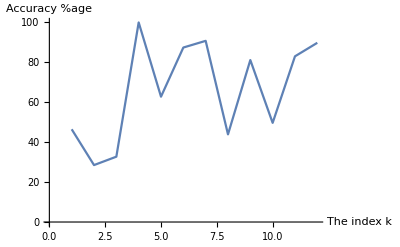

```mathematica
Block[
{accuracy,sum,sum1,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
accuracy={};
For[
n=40,n≤260,n=n+20,
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P];
addtemp=Binomial[n/2,k](-1)^k temp;
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P];
addtemp2=Binomial[n/2,k](-1)^(n/2-k) temp;
If[Abs[addtemp+addtemp2]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp+addtemp2;
]
];
sum1=Sum[Binomial[n/2,k](-1)^k(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P]-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P]k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P])+Binomial[n/2,k](-1)^(n/2-k)(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P]+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P]+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P]),{k,0,n/2}];
Print[k," ",Log[Abs[sum]]/Log[Abs[sum1]]*100];
AppendTo[accuracy,Log[Abs[sum]]/Log[Abs[sum1]]*100];
];
ListLinePlot[accuracy,AxesLabel->{"The index k","Accuracy %age"}]
]
```

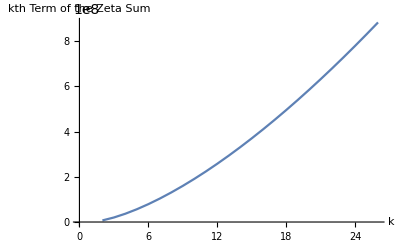

```mathematica
Block[
{accuracy,sum,sum1,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P]-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P]k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P])+Binomial[n/2,k](-1)^(n/2-k)(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P]+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P]+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P])]],{k,0,n/2}],AxesLabel->{"k","kth Term of the Zeta Sum"}]
]
```

```mathematica
Block[
{accuracy,sum,sum1,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P]-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P]k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P])+Binomial[n/2,k](-1)^(n/2-k)(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P]+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P]+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P])]],{k,0,n/2}],AxesLabel->{"k","kth Term of the Zeta Sum"},AxesOrigin->{0,0}]
]
```

-Graphics-

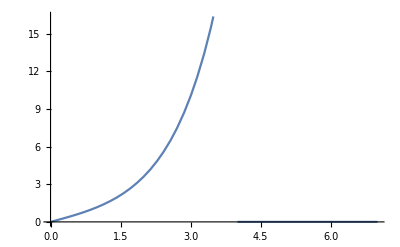

```mathematica
Plot[PDF[ProbabilityDistribution[Sinh[x],{x,0,4}],x],{x,0,7}]
```

```mathematica
Integrate[Sinh[x],{x,0,n/2}]
```

-1+Cosh[n/2]

40 100.

60 100.

80 100.

100 100.

120 100.

140 100.

160 100.

180 100.

200 100.

220 100.

240 100.

260 100.

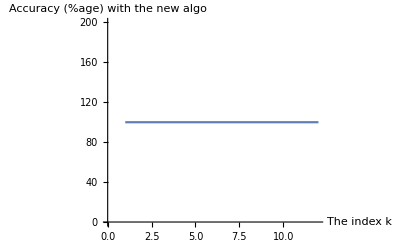

```mathematica
Block[
{accuracy,sum,sum1,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
accuracy={};
For[
n=40,n≤260,n=n+20,
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[Sinh[x]/(Cosh[n/2]-1),{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P];
addtemp=Binomial[n/2,k](-1)^k temp;
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P];
addtemp2=Binomial[n/2,k](-1)^(n/2-k) temp;
If[Abs[addtemp+addtemp2]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp+addtemp2;
]
];
sum1=Sum[Binomial[n/2,k](-1)^k(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P]-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P]k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P])+Binomial[n/2,k](-1)^(n/2-k)(Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P]+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P]+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P]),{k,0,n/2}];
Print[n," ",Log[Abs[sum]]/Log[Abs[sum1]]*100];
AppendTo[accuracy,Log[Abs[sum]]/Log[Abs[sum1]]*100];
];
ListLinePlot[accuracy,AxesLabel->{"The index k","Accuracy (%age) with the new algo"}]
]
```

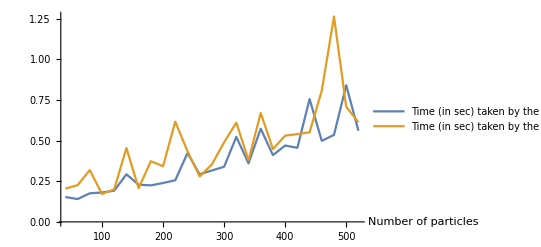

```mathematica
Block[
{timing1,timing2,start,end,sum,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
timing1={};
timing2={};
For[
n=40,n≤520,n=n+20,
sum=0;
storebox={};
start=AbsoluteTime[];
While[True,
k=RandomVariate[ProbabilityDistribution[Sinh[x]/(Cosh[n/2]-1),{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P];
addtemp=Binomial[n/2,k](-1)^k temp;
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P];
addtemp2=Binomial[n/2,k](-1)^(n/2-k) temp;
If[Abs[addtemp+addtemp2]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp+addtemp2;
]
];
end=AbsoluteTime[];
AppendTo[timing1,{n,end-start}];
];
For[
n=40,n≤520,n=n+20,
sum=0;
storebox={};
start=AbsoluteTime[];
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P];
addtemp=Binomial[n/2,k](-1)^k temp;
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P];
addtemp2=Binomial[n/2,k](-1)^(n/2-k) temp;
If[Abs[addtemp+addtemp2]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp+addtemp2;
]
];
end=AbsoluteTime[];
AppendTo[timing2,{n,end-start}];
];
ListLinePlot[{timing1,timing2},AxesLabel->{"Number of particles"},PlotLegends->{"Time (in sec) taken by the new algo","Time (in sec) taken by the old algo"},PlotRange->All]
]
```

```mathematica
Block[
{ZetaGibbs,T,P,kGibbs},
ZetaGibbs[T_,P_]:=Block[
{sum,temp,addtemp,addtemp2,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,m=10^(-26),h=6.63*10^(-34),x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[Sinh[x]/(Cosh[n/2]-1),{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp-k(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3]HypergeometricPFQ[{n/3+4/3},{2/3,4/3},-k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},-k^3(q E0)^3/27/(kB T)^2/P];
addtemp=Binomial[n/2,k](-1)^k temp;
temp=Gamma[n/3+1]HypergeometricPFQ[{n/3+1},{1/3,2/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k (q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3] HypergeometricPFQ[{n/3+4/3},{2/3,4/3},k^3(q E0)^3/27/(kB T)^2/P];
temp=temp+k^2/2 (q E0/kB/T)^2(kB T/P)^(2/3)Gamma[(n+5)/3]HypergeometricPFQ[{n/3+5/3},{4/3,5/3},k^3(q E0)^3/27/(kB T)^2/P];
addtemp2=Binomial[n/2,k](-1)^(n/2-k) temp;
If[Abs[addtemp+addtemp2]/Abs[sum+0.01]<err&&sum>0,
Break[],
sum=sum+addtemp+addtemp2;
]
];
Return[sum/Gamma[n/2+1]^2(kB T/P)^(n/3)(2π m kB T/h^2)^(3n/4)(kB T/q/E0)^(n/2)];
];
kGibbs={};
For[
T=200,T≤500,T+=30,
For[
P=10^5,P≤5*10^6,P+=7*10^5,
Print[{T,P/10^5,ZetaGibbs[T,P],Log[ZetaGibbs[T,P]]}];
AppendTo[kGibbs,{T,P/10^5,Log[ZetaGibbs[T,P]]}]
]
];
ListPlot3D[kGibbs,AxesLabel->{"T(in K)","P(in atm)","-G/kB/T"}]
]
```

{200,1,6.879000351568733499697495478262168`12.961653657589235*^1532192602,3.528003846889432170754×10^9}

{200,8,6.43049711738×10^541711938,1.247337834996766557401×10^9}

{200,15,4.65068985255×10^395610481,9.10926797719819707173×10^8}

{200,22,1.13846532242×10^326664614,7.52173070734735184715×10^8}

{200,29,1.25901476533×10^284521077,6.5513399077314051542×10^8}

{200,36,1.29855006985×10^255365487,5.88000763892613075336×10^8}

{200,43,2.18828171051×10^233657234,5.38015664661738121786×10^8}

{200,50,2.63197256052×10^216684808,4.98935209746810522258×10^8}

{230,1,1.07038741268648693577713989631`12.9626830962962*^1332341412,3.067829474117858785111×10^9}

{230,8,1.30837098203×10^471053875,1.08464163084086340961×10^9}

{230,15,7.54818897924×10^344009128,7.92110292007988229139×10^8}

{230,22,9.38578985442×10^284056199,6.54063571629146974498×10^8}

{230,29,5.03849448839×10^247409645,5.69681762057056154636×10^8}

{230,36,2.80661649936×10^222056958,5.11305042318384561796×10^8}

{230,43,4.48734815296×10^203180216,4.67839738054172204254×10^8}

{230,50,1.5908680833×10^188421585,4.33856733283590314932×10^8}

{260,1,1.5813743379657625682684425442967926249`12.963588156782777*^1178609727,2.713849188306276099374×10^9}

{260,8,6.87626267711×10^416701518,9.59490705502865290306×10^8}

{260,15,9.649270323×10^304315780,7.00712980857737845983×10^8}

{260,22,1.72762693372×10^251280497,5.78594727099083769757×10^8}

{260,29,1.53947380325×10^218862391,5.03949279365074859004×10^8}

{260,36,5.33888055255×10^196435013,4.52308334350907569504×10^8}

{260,43,1.9874943298×10^179736357,4.1385825698413070855×10^8}

{260,50,4.6839964946×10^166680644,3.83796367709199120136×10^8}

{290,1,1.488726904066466997807052768416329`12.964395866043004*^1056684598,2.433106203749127107936×10^9}

{290,8,9.38372601803×10^373594477,8.60233075804083775645×10^8}

{290,15,1.65495455697×10^272834850,6.28225458963040055519×10^8}

{290,22,5.02063639282×10^225285974,5.18740127006600855272×10^8}

{290,29,3.27258432838×10^196221465,4.5181662142003286766×10^8}

{290,36,2.18786513266×10^176114161,4.05517842566679576745×10^8}

{290,43,8.43569681102×10^161142951,3.71045358946142269024×10^8}

{290,50,1.22693992811×10^149437830,3.44093319891901596122×10^8}

{320,1,1.26072950235×10^957620431,2.205002529398823631904×10^9}

{320,8,3.39773153559×10^338570007,7.79586252276197711731×10^8}

{320,15,1.71101011683×10^247256594,5.69329348025964905819×10^8}

{320,22,2.51943672468×10^204165425,4.70108265033829214135×10^8}

{320,29,4.65163784005×10^177825713,4.09458837442056859766×10^8}

{320,36,1.08853081701×10^159603469,3.67500568594366200248×10^8}

{320,43,2.10294761643×10^146035810,3.3625987989265077408×10^8}

{320,50,3.18215989637×10^135428043,3.11834594142716796567×10^8}

{350,1,7.69246287084×10^875538692,2.016002342578946123506×10^9}

{350,8,1.73566976595×10^309549732,7.12764598994895290241×10^8}

{350,15,2.22660787127×10^226063182,5.20529713748479167795×10^8}

{350,22,8.17955034126×10^186665541,4.29813294183906025983×10^8}

{350,29,3.13722970333×10^162583519,3.74362388359254343768×10^8}

{350,36,2.21401929423×10^145923181,3.36000542087681509167×10^8}

{350,43,4.3616039683×10^133518464,3.07437626318702013223×10^8}

{350,50,6.82000796901×10^123819934,2.8510593616376723932×10^8}

{380,1,2.03640771827×10^806417229,1.856844290940152967199×10^9}

{380,8,7.25182964762×10^285111605,6.56493733493860422631×10^8}

{380,15,6.86958243446×10^208216098,4.79435285303290652937×10^8}

{380,22,1.27286843888×10^171928798,3.95880687572457462539×10^8}

{380,29,5.56484389569×10^149747987,3.44807484288535077413×10^8}

{380,36,1.82369225302×10^134402939,3.0947420439685120592×10^8}

{380,43,1.38517217983×10^122977542,2.83166255308073608332×10^8}

{380,50,4.08127752499×10^114044685,2.62597593022611705183×10^8}

{410,1,1.04863494154×10^747411102,1.720977661850941426814×10^9}

{410,8,6.52454359366×10^264249790,6.08457629156378046683×10^8}

{410,15,6.31777294989×10^192980783,4.44354676013485515152×10^8}

{410,22,1.28045334376×10^159348651,3.66913828628524920822×10^8}

{410,29,4.4691557057×10^138790826,3.19577688489129924195×10^8}

{410,36,2.617730568×10^124568586,2.86829770141254524268×10^8}

{410,43,6.65556630862×10^113979193,2.62446792608744824306×10^8}

{410,50,6.60765906898×10^105699960,2.4338315411429635025×10^8}

{440,1,8.94534211691×10^696451264,1.603638300674393624057×10^9}

{440,8,7.30991701972×10^246232768,5.6697190299269319838×10^8}

{440,15,7.21363988863×10^179823011,4.14057786481877962803×10^8}

{440,22,6.83839417397×10^148483978,3.41896996213808767661×10^8}

{440,29,1.04861924831×10^129327824,2.9778831969923187046×10^8}

{440,36,6.67282062772×10^116075281,2.67273213593737637353×10^8}

{440,43,1.37173862817×10^106207893,2.44552711496185660552×10^8}

{440,50,1.51590484272×10^98493153,2.26788866275794286243×10^8}

{470,1,1.30328285434×10^651996939,1.501278432684034485099×10^9}

{470,8,2.43191427925×10^230515792,5.30782227247594808598×10^8}

{470,15,3.98232121642×10^168344955,3.87628585245618305439×10^8}

{470,22,1.31477291704×10^139006286,3.20073802249730874703×10^8}

{470,29,2.49557963352×10^121072864,2.78780572727016466177×10^8}

{470,36,9.95903157904×10^108666228,2.50213239003172006791×10^8}

{470,43,3.21558580196×10^99428673,2.28942981433989109361×10^8}

{470,50,4.51946891056×10^92206363,2.12312998431392222457×10^8}

{500,1,3.03428675244×10^612877132,1.411201749090120401357×10^9}

{500,8,1.54359133812×10^216684853,4.98935312829517858101×10^8}

{500,15,1.57134509791×10^158244266,3.64370888395316504461×10^8}

{500,22,4.28421877066×10^130665916,3.00869391798950380044×10^8}

{500,29,1.07579734117×10^113808500,2.6205375562907494759×10^8}

{500,36,4.1157414977×10^102146262,2.35200461601083166627×10^8}

{500,43,2.16791252341×10^93462960,2.15206419216863505788×10^8}

{500,50,9.45725080842×10^86673988,1.99574234965926528298×10^8}

-Graphics3D-